## Init

Use this to set your Census API key:

```mathematica
(*SystemCredential["USCensusAPIKey"]="..."*)
```

Set directories to save intermediate data:

```mathematica
$dataDirectory=FileNameJoin[{NotebookDirectory[],"data"}];
```

## Census API

Utilities for getting data from the Census API.

```mathematica
$defaultACSVintage="2022";
$defaultDecennialVintage="2020";
```

### Base

```mathematica
Options[censusQuery]={
Authentication:>SystemCredential["USCensusAPIKey"],
"APIBase"->"api.census.gov"
};
```

```mathematica
censusQuery[path_,query_,opts:OptionsPattern[]]:=
Enclose@Module[{rawResponse},
rawResponse=Confirm@Import[HTTPRequest[<|
"Scheme"->"HTTPS",
"Domain"->OptionValue["APIBase"],
"Path"->path,
"Query"->Join[
query,
{"key"->OptionValue[Authentication]}
]
|>]];
If[Length[rawResponse]===0,Return[<||>]];
AssociationThread[First[rawResponse],#]&/@Rest[rawResponse]
]
```

### ACS data

```mathematica
acsCategoriesCodes=<|
"WhiteAlone"->"A",
"BlackOrAfricanAmericanAlone"->"B",
"AsianAlone"->"D",
"AmericanIndianAndAlaskaNativeAlone"->"C",
"NativeHawaiianAndOtherPacificIslanderAlone"->"E",
"SomeOtherRaceAlone"->"F",
"TwoOrMore"->"G",
"HispanicOrLatino"->"I",
"WhiteAloneNotHispanicOrLatino"->"H",
"Overall"->""
|>;
```

The B05003 tables (Sex by Age by Nativity and Citizenship Status) are the same ones mentioned in Moon's GA expert report.

Get the estimate variables:

```mathematica
getVAPVarsACS[r0_]:=
With[{r=Replace[r0,acsCategoriesCodes]},
{
"B05003"<>r<>"_008E",
"B05003"<>r<>"_019E"
}
]
getVAPVarsACS[r0_List]:=Union@@(getVAPVarsACS/@r0)

getCVAPVarsACS[r0_]:=
With[{r=Replace[r0,acsCategoriesCodes]},
{
"B05003"<>r<>"_009E",
"B05003"<>r<>"_011E",
"B05003"<>r<>"_020E",
"B05003"<>r<>"_022E"
}
]
getCVAPVarsACS[r0_List]:=Union@@(getCVAPVarsACS/@r0)
```

Get the margin of error variables:

```mathematica
getVAPErrorVarsACS[r0_]:=
With[{r=Replace[r0,acsCategoriesCodes]},
{
"B05003"<>r<>"_008M",
"B05003"<>r<>"_019M"
}
]
getVAPErrorVarsACS[r0_List]:=Union@@(getVAPErrorVarsACS/@r0)

getCVAPErrorVarsACS[r0_]:=
With[{r=Replace[r0,acsCategoriesCodes]},
{
"B05003"<>r<>"_009M",
"B05003"<>r<>"_011M",
"B05003"<>r<>"_020M",
"B05003"<>r<>"_022M"
}
]
getCVAPErrorVarsACS[r0_List]:=Union@@(getCVAPErrorVarsACS/@r0)
```

The ACS API reports estimates of the margin of error (MoE) for every reported variable. However, we use sums of several ACS variables.

The best way to estimate the MoE for the sum of ACS variables is using variance replicate tables, which can be used to estimate margins of error in the same way that the MoEs are computed in the API tables.

However, the variance replicate tables for the particular ACS variable of interest (B05003) is not broken down by race and ethnicity. Therefore, we instead use a method for estimating the MoE given by the Census Bureau that merely composes the MoE from the API.

```mathematica
getACSTractsRaw[state_,r_,year_:$defaultACSVintage]:=
Module[{rawResponse,rawAcsData,vapVars,cvapVars},
vapVars=Join[getVAPVarsACS[r],getVAPErrorVarsACS[r]];
cvapVars=Join[getCVAPVarsACS[r],getCVAPErrorVarsACS[r]];
rawAcsData=censusQuery[
{"data",year,"acs","acs5"},
{
"get"->StringRiffle[Join[vapVars,cvapVars],","],
"for"->"tract:*",
"in"->"state:"<>Replace[state,_Entity:>state["FIPSCode"]],
"in"->"county:*"
}
];
Association[
#state<>#county<>#tract->Join@@Map[
c|-><|
{c,"VAP"}->Total@ToExpression@Lookup[#,getVAPVarsACS[c]],
{c,"CVAP"}->Total@ToExpression@Lookup[#,getCVAPVarsACS[c]],
{c,"VAPError"}->Sqrt@Total[N@ToExpression@Lookup[#,getVAPErrorVarsACS[c]]^2],
{c,"CVAPError"}->Sqrt@Total[N@ToExpression@Lookup[#,getCVAPErrorVarsACS[c]]^2]
|>,
Flatten[{r}]
]&/@rawAcsData
]
]
getACSTracts[state_,r_,year_:$defaultACSVintage]:=Merge[BlockMap[getACSTractsRaw[state,#,year]&,r,UpTo[4]],Merge[Last]]
```

```mathematica
geoidTract[geoid_]:=StringTake[geoid,11]
geoidState[geoid_]:=StringTake[geoid,2]
```

### Decennial data

```mathematica
getDecennialBlocksRaw[state_,vars_,year_]:=
Module[{rawResponse,rawDecData},
rawDecData=censusQuery[
{"data",year,"dec","pl"},
{
"get"->StringRiffle[vars,","],
"for"->"block:*",
"in"->"state:"<>Replace[state,_Entity:>state["FIPSCode"]],
"in"->"county:*",
"in"->"tract:*"
}
];
Association[#state<>#county<>#tract<>#block->ToExpression[KeyDrop[#,{"state","county","tract","block"}]]&/@rawDecData]
]
getDecennialBlocks[state_,vars_,year_:$defaultDecennialVintage]:=Merge[BlockMap[getDecennialBlocksRaw[state,#,year]&,vars,UpTo[50]],Merge[Last]]
```

```mathematica
getDecennialTractsRaw[state_,vars_,year_]:=
Module[{rawResponse,rawDecData},
rawDecData=censusQuery[
{"data",year,"dec","pl"},
{
"get"->StringRiffle[vars,","],
"for"->"tract:*",
"in"->"state:"<>Replace[state,_Entity:>state["FIPSCode"]],
"in"->"county:*"
}
];
Association[#state<>#county<>#tract->ToExpression[KeyDrop[#,{"state","county","tract"}]]&/@rawDecData]
]
getDecennialTracts[state_,vars_,year_:$defaultDecennialVintage]:=Merge[BlockMap[getDecennialTractsRaw[state,#,year]&,vars,UpTo[50]],Merge[Last]]
```

## Congressional districts

Get the partition of blocks into the congressional districts of the 118th Congress.

From https://www.census.gov/geographies/mapping-files/2023/dec/rdo/118-congressional-district-bef.html

```mathematica
rawZip=URLRead["https://www2.census.gov/programs-surveys/decennial/rdo/mapping-files/2023/118-congressional-district-bef/cd118.zip"];
```

```mathematica
blockDistrictPairs={#[[1]],{geoidState[#[[1]]],#[[2]]}}&/@Rest@Import[rawZip,{"ZIP","National_CD118.txt","CSV","RawData"}];
```

```mathematica
blockDistrictPairs:=blockDistrictPairs=;
```

```mathematica
districtAggregate[vals_,districtPairs_,agg_:Total]:=KeySort[agg[vals[[#]]]&/@GroupBy[districtPairs,Last->First]]
```

### Moon data

This is a version of the Georgia congressional districts from Moon, from a file called GaCongEnacted.csv:

```mathematica
georgiaBlockDistrictPairs=Rest@Import[FileNameJoin[{NotebookDirectory[],"moonData","GaCongEnacted.csv"}],"Numeric"->False];
```

```mathematica
georgiaBlockDistrictPairs=;
```

The districting from Moon is identical to the one from the Census Bureau:

```mathematica
KeySort@KeyMap[ToExpression]@GroupBy[Select[blockDistrictPairs,MatchQ[{_,{"13",_}}]],(#[[2,2]]&)->First,Sort]===KeySort@KeyMap[ToExpression]@GroupBy[georgiaBlockDistrictPairs,Last->First,Sort]
```

True

## Beta-binomial proportion estimation

In approximate form, the generative model is:

p_t\[Distributed]BetaDistribution[r*c,(1-r)*c]
CVAP_t\[Distributed]BinomialDistribution[VAP_t,p_t]
CVAP_b\[Distributed]BinomialDistribution[VAP_b,p_t_b]

Where r and c are estimated with MLE, variables subscripted with t are indexed by tract and b indexed by block, p_t is the citizenship rate of a tract, and t_b is the tract enclosing a block b.

(TODO: It might be good to pick better variable names.)

### Beta binomial utilities

```mathematica
betaBinomialCount[BetaDistribution[a_,b_],n_]:=BetaBinomialDistribution[a,b,n]
```

### MLE

A convenience function for numerically evaluating the log beta in a more stable way:

```mathematica
logBeta[a_,b_]:=LogGamma[a]+LogGamma[b]-LogGamma[a+b]
```

The function for computing the MLE of the r and c parameters in the model:

```mathematica
proportionsMLE[ps_]:=
Module[{r,c},
{r,c}/.NMaximize[{
Total[
If[#1>0,
N@LogLikelihood[BetaBinomialDistribution[r*c,(1-r)*c,#2],{#1}],
0
]&@@@ps
]/.Log[Beta[a_,b_]]:>logBeta[a,b],
0<=r<=1,
0<c
},
{r,c}
][[2]]
]
```

ps is taken to be a list of pairs with the subpopulation in the first position, and the population in the second position.

#### Alternative version

Alternatively, we could compute the a and b parameters directly instead of r and c:

```mathematica
proportionsMLE2[ps_]:=
Module[{a,b},
{a,b}/.NMaximize[{
Total[
If[#1>0,
N@LogLikelihood[BetaBinomialDistribution[a,b,#2],{#1}],
0
]&@@@ps
]/.Log[Beta[x_,y_]]:>logBeta[x,y],
a>0,
b>0
},
{a,b}
][[2]]
]
```

### Conjugacy

Get the distribution for the statewide citizenship rate given r and c:

```mathematica
mleDistribution[{r_,c_}]:=BetaDistribution[r*c,(1-r)*c]
```

Get the estimated CVAP distribution for a tract (a slightly weird function):

```mathematica
countDistribution[p_,{r_,c_}]:=BetaBinomialDistribution[r*c+p[[1]],(1-r)*c+(p[[2]]-p[[1]]),p[[2]]]
```

Get the estimated citizenship rate for a tract, given its VAP and CVAP, and the r and c of its enclosing state:

```mathematica
proportionDistribution[p_,{r_,c_}]:=BetaDistribution[r*c+p[[1]],(1-r)*c+(p[[2]]-p[[1]])]
```

```mathematica
betaBinomialProportionEstimate[ps_]:=With[{p=proportionsMLE[ps]},proportionDistribution[#,p]&/@ps]
```

```mathematica
(*getBlockCVAPDistribution[blockVap_,tractP:BetaDistribution[a_,b_]]:=BetaBinomialDistribution[a,b,blockVap]*)
```

## Categories

### Decennial variables

From the decennial variables, we can derive a disjoint and covering set of race/ethnicity categories. However, this requires some work because, as given, the decennial variables are not disjoint. (In particular, P3 covers the VAP, while P4 covers non-Hispanic VAP. These overlap (they both include non-Hispanic VAP), but disjoint categories can be derived.)

Get the list of P3 and P4 variables:

```mathematica
p3Variables=Import["https://api.census.gov/data/2020/dec/pl/groups/P3.json","RawJSON"]["variables"];
```

```mathematica
p4Variables=Import["https://api.census.gov/data/2020/dec/pl/groups/P4.json","RawJSON"]["variables"];
```

```mathematica
p3Variables=;
p4Variables=;
```

For each variable, get which race categories are included:

```mathematica
variableLabelRaceCategories[label_]:=KeySort@<|
"White"->StringContainsQ[label,"White"],
"BlackOrAfricanAmerican"->StringContainsQ[label,"Black or African American"],
"Asian"->StringContainsQ[label,"Asian"],
"AmericanIndianAndAlaskaNative"->StringContainsQ[label,"American Indian and Alaska Native"],
"NativeHawaiianAndOtherPacificIslander"->StringContainsQ[label,"Native Hawaiian and Other Pacific Islander"],
"SomeOtherRace"->StringContainsQ[label,"Some Other Race"]
|>
```

```mathematica
p3VariableRaceCategories=KeySort@
Map[variableLabelRaceCategories[#label]&]@
Select[Or@@variableLabelRaceCategories[#label]&]@
KeySelect[Not@*StringEndsQ["A"]]@
p3Variables;
```

```mathematica
p4VariableRaceCategories=KeySort@
Map[variableLabelRaceCategories[#label]&]@
Select[Or@@variableLabelRaceCategories[#label]&]@
KeySelect[Not@*StringEndsQ["A"]]@
p4Variables;
```

A DerivedCensusVariable represents the difference between two sets of variables. This is needed because P3 represents all people, while P4 represents non-Hispanic people. Therefore, the number of Hispanic people is given by the difference between P3 and P4.

```mathematica
censusVariables=Join[
KeyMap[KeySort@*Append["HispanicOrLatino"->True]]@Merge[{
AssociationMap[Reverse,p3VariableRaceCategories],
AssociationMap[Reverse,p4VariableRaceCategories]
},
DerivedCensusVariable[{#[[1]]},{#[[2]]}]&
],
KeyMap[KeySort@*Append["HispanicOrLatino"->False]]@Map[DerivedCensusVariable[{#},{}]&]@AssociationMap[Reverse]@p4VariableRaceCategories
];
```

```mathematica
decennialCategory[cat_]:=
Values@KeySelect[
censusVariables,
MatchQ@KeySort@Join[
<|
"White"->_,
"BlackOrAfricanAmerican"->_,
"Asian"->_,
"AmericanIndianAndAlaskaNative"->_,
"NativeHawaiianAndOtherPacificIslander"->_,
"SomeOtherRace"->_,
"HispanicOrLatino"->_
|>,
cat
]
]
```

### ACS and litigation categories

Encode the ACS and target categories:

```mathematica
acsCategories=<|
"WhiteAlone"->decennialCategory[<|
"White"->True,
"BlackOrAfricanAmerican"->False,
"Asian"->False,
"AmericanIndianAndAlaskaNative"->False,
"NativeHawaiianAndOtherPacificIslander"->False,
"SomeOtherRace"->False
|>],
"BlackOrAfricanAmericanAlone"->decennialCategory[<|
"White"->False,
"BlackOrAfricanAmerican"->True,
"Asian"->False,
"AmericanIndianAndAlaskaNative"->False,
"NativeHawaiianAndOtherPacificIslander"->False,
"SomeOtherRace"->False
|>],
"AsianAlone"->decennialCategory[<|
"White"->False,
"BlackOrAfricanAmerican"->False,
"Asian"->True,
"AmericanIndianAndAlaskaNative"->False,
"NativeHawaiianAndOtherPacificIslander"->False,
"SomeOtherRace"->False
|>],
"AmericanIndianAndAlaskaNativeAlone"->decennialCategory[<|
"White"->False,
"BlackOrAfricanAmerican"->False,
"Asian"->False,
"AmericanIndianAndAlaskaNative"->True,
"NativeHawaiianAndOtherPacificIslander"->False,
"SomeOtherRace"->False
|>],
"NativeHawaiianAndOtherPacificIslanderAlone"->decennialCategory[<|
"White"->False,
"BlackOrAfricanAmerican"->False,
"Asian"->False,
"AmericanIndianAndAlaskaNative"->False,
"NativeHawaiianAndOtherPacificIslander"->True,
"SomeOtherRace"->False
|>],
"SomeOtherRaceAlone"->decennialCategory[<|
"White"->False,
"BlackOrAfricanAmerican"->False,
"Asian"->False,
"AmericanIndianAndAlaskaNative"->False,
"NativeHawaiianAndOtherPacificIslander"->False,
"SomeOtherRace"->True
|>],
"TwoOrMore"->Values@KeySelect[censusVariables,Count[KeyDrop[#,"HispanicOrLatino"],True]>=2&],
"HispanicOrLatino"->decennialCategory[<|"HispanicOrLatino"->True|>],
"WhiteAloneNotHispanicOrLatino"->decennialCategory[<|
"White"->True,
"BlackOrAfricanAmerican"->False,
"Asian"->False,
"AmericanIndianAndAlaskaNative"->False,
"NativeHawaiianAndOtherPacificIslander"->False,
"SomeOtherRace"->False,
"HispanicOrLatino"->False
|>]
|>;
```

```mathematica
litigationCategories=<|
"LitigationBlack"->decennialCategory[<|
"BlackOrAfricanAmerican"->True
|>],
"LitigationHispanic"->decennialCategory[<|
"BlackOrAfricanAmerican"->False,
"HispanicOrLatino"->True
|>],
"LitigationAsianOrPacificIslander"->Union[
decennialCategory[<|
"BlackOrAfricanAmerican"->False,
"HispanicOrLatino"->False,
"Asian"->True
|>],
decennialCategory[<|
"BlackOrAfricanAmerican"->False,
"HispanicOrLatino"->False,
"NativeHawaiianAndOtherPacificIslander"->True
|>]
],
"LitigationAmericanIndian"->decennialCategory[<|
"BlackOrAfricanAmerican"->False,
"HispanicOrLatino"->False,
"Asian"->False,
"NativeHawaiianAndOtherPacificIslander"->False,
"AmericanIndianAndAlaskaNative"->True
|>],
"LitigationSomeOtherRace"->decennialCategory[<|
"BlackOrAfricanAmerican"->False,
"HispanicOrLatino"->False,
"Asian"->False,
"NativeHawaiianAndOtherPacificIslander"->False,
"AmericanIndianAndAlaskaNative"->False,
"SomeOtherRace"->True
|>],
"LitigationWhite"->decennialCategory[<|
"BlackOrAfricanAmerican"->False,
"HispanicOrLatino"->False,
"Asian"->False,
"NativeHawaiianAndOtherPacificIslander"->False,
"AmericanIndianAndAlaskaNative"->False,
"SomeOtherRace"->False,
"White"->True
|>]
|>;
```

The target categories are disjoint:

```mathematica
Select[
Subsets[Keys[litigationCategories],{2}],
Apply[IntersectingQ[litigationCategories[#1],litigationCategories[#2]]&]
]
```

{}

The ACS categories are not disjoint, mostly because many categories intersect with HispanicOrLatino:

```mathematica
Select[
Subsets[Keys[acsCategories],{2}],
Apply[IntersectingQ[acsCategories[#1],acsCategories[#2]]&]
]
```

{{WhiteAlone,HispanicOrLatino},{WhiteAlone,WhiteAloneNotHispanicOrLatino},{BlackOrAfricanAmericanAlone,HispanicOrLatino},{AsianAlone,HispanicOrLatino},{AmericanIndianAndAlaskaNativeAlone,HispanicOrLatino},{NativeHawaiianAndOtherPacificIslanderAlone,HispanicOrLatino},{SomeOtherRaceAlone,HispanicOrLatino},{TwoOrMore,HispanicOrLatino}}

The target categories cover everything:

```mathematica
Complement[Values@censusVariables,Catenate@Values@litigationCategories]
```

{}

### Decennial population tensors

Get the set of variables needed to construct the race/ethnicity population tensor:

```mathematica
categoryVariables[DerivedCensusVariable[pos_,neg_]]:=Union[pos,neg]
categoryVariables[l_List]:=Union@@(categoryVariables/@l)
```

```mathematica
allDecennialVariables=Union@@(categoryVariables/@acsCategories);
```

categoryTotal takes a population tensor and a race/ethnicity category, and returns the number of people in that category:

```mathematica
categoryTotal[decData_,DerivedCensusVariable[pos_,neg_]]:=Total[Lookup[decData,pos]]-Total[Lookup[decData,neg]]
categoryTotal[decData_,l_List]:=Total[categoryTotal[decData,#]&/@l]
```

For computing conditional probabilities:

```mathematica
categoryConditional[decData_,p_,q_]:=categoryTotal[decData,Intersection[p,q]]/categoryTotal[decData,q]
```

## Category conversion

The ACS gives us VAP and CVAP for the ACS categories. However, these are different from the categories that are relevant for litigation. In this section, we derive estimates of VAP and CVAP for the litigation categories from the numbers for ACS categories.

### Visualization utilities

```mathematica
{rH,rB,r2}=N@{
Disk[{0,1},2],
Disk[{-Sqrt[3]/2,-1/2},2],
Disk[{Sqrt[3]/2,-1/2},2]
};
```

```mathematica
vennDiagramRegion[f_,rs_,0]:=BoundaryDiscretizeRegion@BooleanRegion[f,rs]
vennDiagramRegion[f_,rs_,t_:0.05]:=RegionErosion[vennDiagramRegion[f,rs,0],t]
```

```mathematica
baseVennDiagram[c_]:={
FaceForm[],
{EdgeForm[Black],{rH,rB,r2}},
{EdgeForm[{Thick,Blue}],
vennDiagramRegion[#2&&!#3&,{rH,rB,r2}]},
MapThread[Inset[Style[#1,Large],#2]&,{{"H+",c<>"+","2+"},(RegionCentroid/@{rH,rB,r2})*3.5}],,
{Blue,Inset[Style[c,Large],RegionCentroid[rB]*3.7+{0,2}]}
};
```

Below is a Venn diagram showing how the Hispanic or Latino (H), Black Alone (B), and Two Or More (2+) categories relate:

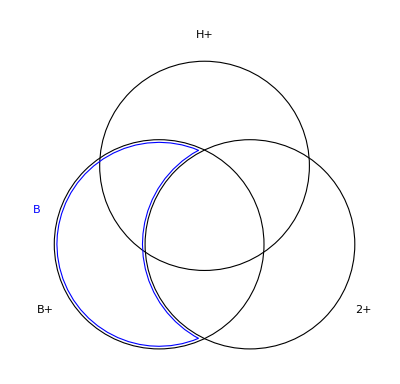

```mathematica
Graphics[baseVennDiagram["B"]]
```

### Explanations

#### B+∪ H+

If the goal is to get any part Black or Hispanic, then the target region is shown in red:

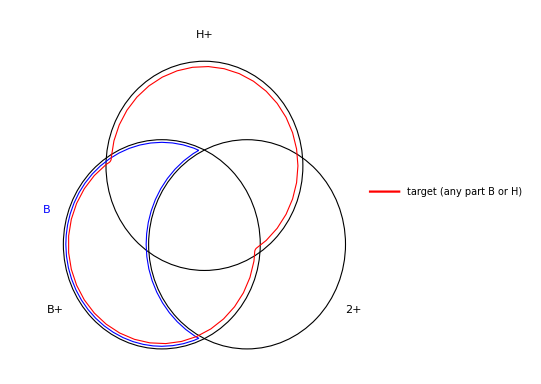

```mathematica
Legended[
Graphics[{
baseVennDiagram["B"],
FaceForm[],
{EdgeForm[{Thick,Red}],vennDiagramRegion[#1||#2&,{rH,rB,r2},0.1]}
}],
LineLegend[{Red},{"target (any part B or H)"}]
]
```

A naive way to get this red region is to add the VAP/CVAP numbers for H+ with B, which are both given by the ACS. However, this double counts B∩H+ and doesn't count B+∪2+:

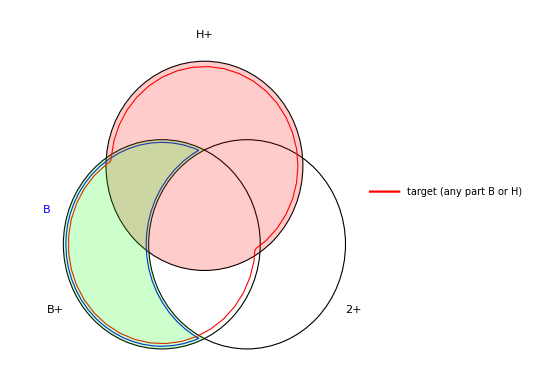

```mathematica
Legended[
Graphics[{
baseVennDiagram["B"],
FaceForm[],
{EdgeForm[{Thick,Red}],vennDiagramRegion[#1||#2&,{rH,rB,r2},0.1]},
{
Opacity[0.2],
FaceForm[Red],vennDiagramRegion[#1&,{rH,rB,r2},0],
FaceForm[Green],vennDiagramRegion[#2&&!#3&,{rH,rB,r2},0]
}
}],
LineLegend[{Red},{"target (any part B or H)"}]
]
```

The double counted region can be approximated by N(H+)p(B|H+) or N(B)p(H+|B). These can both be computed because N(H+) and N(B) are available through the ACS, while p(B|H+) and p(H+|B) are available through the decennial census. The uncounted region can be approximated with N(2+)p(B+∧¬H+|2+). Thus, the target category can be approximated with:

N(H+)+N(B)-N(H+)p(B|H+)+N(2+)p(B+∧¬H+|2+)
or
N(H+)+N(B)-N(B)p(H+|B)+N(2+)p(B+∧¬H+|2+)

The first assumes that the citizenship rate among people who are in B∩H+ is the citizenship rate among H+, while the second assumes it equals the citizenship rate among B.

There are three regions where we have two ways to calculate them by assigning them citizenship rates from H+, 2+, or B. There are a few naive policies for these regions that we have discussed in the past:

Assume that the citizenship rate among people from two ACS categories is equal to the mean of the citizenship rates of the categories.

Take a weighted mean of the citizenship rates of the contained ACS categories based on what proportion of the ACS category is made up of people from the target category. (That is, if 90% of Asians are Hispanic, but only 10% of Hispanics are Asian, then the citizenship rate among Asian Hispanics might be closer to that of Asians that Hispanics.)

Proposed by Moon: Anytime the overlap includes H+, just use the rate from H+.

#### B+

To get just B+ we can use N(B) and add all those in 2+ who are under counted:

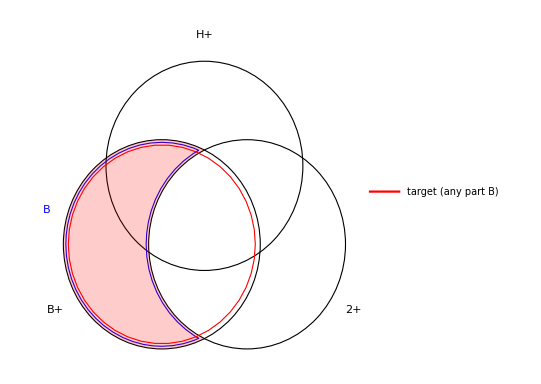

```mathematica
Legended[
Graphics[{
baseVennDiagram["B"],
FaceForm[],
{EdgeForm[{Thick,Red}],vennDiagramRegion[#2&,{rH,rB,r2},0.1]},
{
Opacity[0.2],
FaceForm[Red],vennDiagramRegion[#2&&!#3&,{rH,rB,r2},0]
}
}],
LineLegend[{Red},{"target (any part B)"}]
]
```

Thus, N(B+) can be estimated with:

N(B)+N(2+)p(B+|2+)

We could also use H+ to help estimate N(2+∩B∩H), but then there would be a lot more double counting to subtract off.

#### H+ (but not B+)

A bit similarly to B+, we just use N(H+) and subtract anyone also in B+, which can be estimated with N(H+)p(B+|H+):

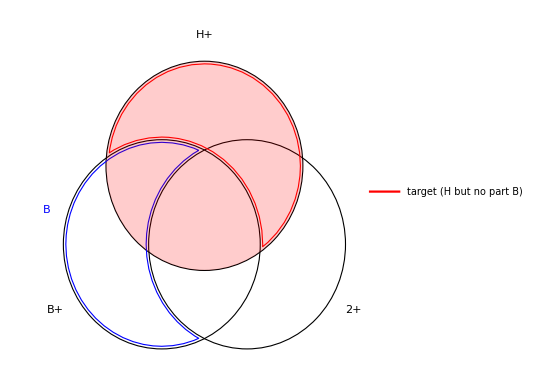

```mathematica
Legended[
Graphics[{
baseVennDiagram["B"],
FaceForm[],
{EdgeForm[{Thick,Red}],vennDiagramRegion[#1&&!#2&,{rH,rB,r2}]},
{
Opacity[0.2],
FaceForm[Red],vennDiagramRegion[#1&,{rH,rB,r2},0]
}
}],
LineLegend[{Red},{"target (H but no part B)"}]
]
```

Thus, the whole value can be estimated with:

N(H+)-N(H+)p(B+|H+)
or
N(H+)-N(B)p(H+|B)-N(2+)p(H+∧B+|2+)

#### X+

For all other target categories, we get something like this:

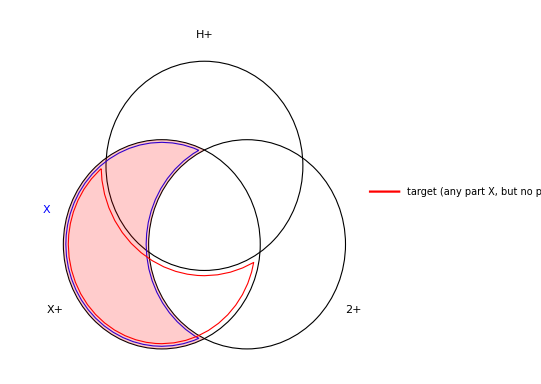

```mathematica
Legended[
Graphics[{
baseVennDiagram["X"],
FaceForm[],
{EdgeForm[{Thick,Red}],vennDiagramRegion[#2&&!#1&,{rH,rB,r2},0.1]},
{
Opacity[0.2],
FaceForm[Red],vennDiagramRegion[#2&&!#3&,{rH,rB,r2},0]
}
}],
LineLegend[{Red},{"target (any part X, but no part anything earlier)"}]
]
```

We can estimate the target area with N(X), which over counts by including too much of H and under counts by missing parts of 2+. We can subtract the extra parts of H+ with N(X)p(H+|X) or N(H+)p(X|H+). We can add the extra parts of 2+ by adding N(2+)p(T|2+) where T is the target category (with the red outline). Thus, the final formula can be written as:

N(X)-N(X)p(H+|X)+N(2+)p(T|2+)
or
N(X)-N(H+)p(X|H+)+N(2+)p(T|2+)

#### Estimates of all overlap regions

```mathematica
Canvas[Graphics[baseVennDiagram["X"]]]
```

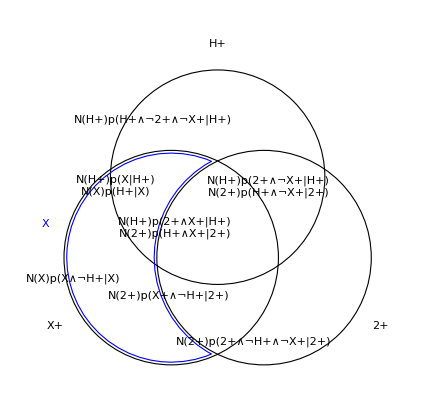

### Note on computing proportions

When computing proportions like p(B|H+)=(N_dec(B∧H+))/(N_dec(H+)), we run into problems when N_dec(H+)=0. This wouldn't be a problem if N_ACS(H+)=0, but that often isn't the case. This is the same problem that we have when estimating citizenship rates, which we solved with the beta-binomial model.

### Note on clipping

Some of these category conversions can lead to impossible VAP/CVAP. For example, consider this estimate for VAP/CVAP:

N(X)-N(H+)p(X|H+)+N(2+)p(T|2+)

If the decennial census says that a large proportion of H+ are also X, then p(X|H+) will be large. If N(H+) is also large, then the negative term will be large. However, N(X) could still be small, leading to a negative estimate of VAP/CVAP. This is impossible, so we clip the VAP and CVAP estimates so that 0<=VAP and 0<=CVAP<=VAP.

```mathematica
clipVAP[{cvap0_,vap0_}]:=
With[{vap=Clip[vap0,{0,Infinity}]},{Clip[cvap0,{0,vap}],vap}]
clipVAP[a_?AssociationQ]:=clipVAP/@a
clipVAP[l_List]:=clipVAP/@l
```

TODO: Arguably clipping should be done on the intermediate expressions, and not just the total output. -- AS argued this.

## Category conversion implementation

```mathematica
betaBinomialCategoryConditionals[decData_,p_,q_]:=
Mean/@betaBinomialProportionEstimate[{
categoryTotal[#,Intersection[p,q]],
categoryTotal[#,q]
}&/@decData]
```

```mathematica
categoryVAPCVAP[acsTracts_,acsCat_]:=Merge[{
acsTracts[[All,Key[{acsCat,"CVAP"}]]],
acsTracts[[All,Key[{acsCat,"VAP"}]]]
},Identity]
```

```mathematica
seperateCategoryVAPCVAP[vapcvap_,cat_]:=Transpose@<|{cat,"CVAP"}->vapcvap[[All,1]],{cat,"VAP"}->vapcvap[[All,2]]|>
```

### Variant 1

```mathematica
(*N(X)-N(X)p(H+|X)+N(2+)p(T|2+)*)
litigationCategoryGeneralEstimate1[acsTracts_,decennialTracts_,acsCats_,litCat_]:=
clipVAP[
Total[categoryVAPCVAP[acsTracts,#]&/@acsCats]-
Total[categoryVAPCVAP[acsTracts,#]&/@acsCats]*betaBinomialCategoryConditionals[decennialTracts,acsCategories["HispanicOrLatino"],Union@@(acsCategories/@acsCats)]+
categoryVAPCVAP[acsTracts,"TwoOrMore"]*betaBinomialCategoryConditionals[decennialTracts,litCat,acsCategories["TwoOrMore"]]
]
```

```mathematica
litigationCategoryEstimate1[acsTracts_,decennialTracts_]:=
Merge[{
(*N(B)+N(2+)p(B+|2+)*)
seperateCategoryVAPCVAP[
clipVAP[
categoryVAPCVAP[acsTracts,"BlackOrAfricanAmericanAlone"]+
categoryVAPCVAP[acsTracts,"TwoOrMore"]*betaBinomialCategoryConditionals[decennialTracts,litigationCategories["LitigationBlack"],acsCategories["TwoOrMore"]]
],
"LitigationBlack"
],

(*N(H+)-N(H+)p(B+|H+)*)
seperateCategoryVAPCVAP[
clipVAP[
categoryVAPCVAP[acsTracts,"HispanicOrLatino"]-
categoryVAPCVAP[acsTracts,"HispanicOrLatino"]*betaBinomialCategoryConditionals[decennialTracts,litigationCategories["LitigationBlack"],acsCategories["HispanicOrLatino"]]
],
"LitigationHispanic"
],

seperateCategoryVAPCVAP[
litigationCategoryGeneralEstimate1[acsTracts,decennialTracts,{"AsianAlone","NativeHawaiianAndOtherPacificIslanderAlone"},litigationCategories["LitigationAsianOrPacificIslander"]],
"LitigationAsianOrPacificIslander"
],

seperateCategoryVAPCVAP[
litigationCategoryGeneralEstimate1[acsTracts,decennialTracts,{"AmericanIndianAndAlaskaNativeAlone"},litigationCategories["LitigationAmericanIndian"]],
"LitigationAmericanIndian"
],

seperateCategoryVAPCVAP[
litigationCategoryGeneralEstimate1[acsTracts,decennialTracts,{"SomeOtherRaceAlone"},litigationCategories["LitigationSomeOtherRace"]],
"LitigationSomeOtherRace"
],

seperateCategoryVAPCVAP[Values/@acsTracts[[All,{Key[{"WhiteAloneNotHispanicOrLatino","CVAP"}],Key[{"WhiteAloneNotHispanicOrLatino","VAP"}]}]],
"LitigationWhite"
]

},Apply[Join]];
```

### Variant 2

```mathematica
(*N(X)-N(H+)p(X|H+)+N(2+)p(T|2+)*)
litigationCategoryGeneralEstimate2[acsTracts_,decennialTracts_,acsCats_,litCat_]:=
clipVAP[
Total[categoryVAPCVAP[acsTracts,#]&/@acsCats]-
categoryVAPCVAP[acsTracts,"HispanicOrLatino"]*betaBinomialCategoryConditionals[decennialTracts,Union@@(acsCategories/@acsCats),acsCategories["HispanicOrLatino"]]+
categoryVAPCVAP[acsTracts,"TwoOrMore"]*betaBinomialCategoryConditionals[decennialTracts,litCat,acsCategories["TwoOrMore"]]
]
```

```mathematica
litigationCategoryEstimate2[acsTracts_,decennialTracts_]:=
Merge[{
(*N(B)+N(2+)p(B+|2+)*)
seperateCategoryVAPCVAP[
clipVAP[
categoryVAPCVAP[acsTracts,"BlackOrAfricanAmericanAlone"]+
categoryVAPCVAP[acsTracts,"TwoOrMore"]*betaBinomialCategoryConditionals[decennialTracts,litigationCategories["LitigationBlack"],acsCategories["TwoOrMore"]]
],
"LitigationBlack"
],

(*N(H+)-N(H+)p(B+|H+)*)
seperateCategoryVAPCVAP[
clipVAP[
categoryVAPCVAP[acsTracts,"HispanicOrLatino"]-
categoryVAPCVAP[acsTracts,"HispanicOrLatino"]*betaBinomialCategoryConditionals[decennialTracts,litigationCategories["LitigationBlack"],acsCategories["HispanicOrLatino"]]
],
"LitigationHispanic"
],

seperateCategoryVAPCVAP[
litigationCategoryGeneralEstimate2[acsTracts,decennialTracts,{"AsianAlone","NativeHawaiianAndOtherPacificIslanderAlone"},litigationCategories["LitigationAsianOrPacificIslander"]],
"LitigationAsianOrPacificIslander"
],

seperateCategoryVAPCVAP[
litigationCategoryGeneralEstimate2[acsTracts,decennialTracts,{"AmericanIndianAndAlaskaNativeAlone"},litigationCategories["LitigationAmericanIndian"]],
"LitigationAmericanIndian"
],

seperateCategoryVAPCVAP[
litigationCategoryGeneralEstimate2[acsTracts,decennialTracts,{"SomeOtherRaceAlone"},litigationCategories["LitigationSomeOtherRace"]],
"LitigationSomeOtherRace"
],

seperateCategoryVAPCVAP[Values/@acsTracts[[All,{Key[{"WhiteAloneNotHispanicOrLatino","CVAP"}],Key[{"WhiteAloneNotHispanicOrLatino","VAP"}]}]],
"LitigationWhite"
]

},Apply[Join]];
```

### Variant 3

```mathematica
litigationCategoryEstimate3[acsTracts_,decennialTracts_]:=Mean[{
litigationCategoryEstimate1[acsTracts,decennialTracts],
litigationCategoryEstimate2[acsTracts,decennialTracts]
}]
```

## Sum distributions

There are two ways to do this: with explicit convolutions, or by using the convolution theorem with Fourier transforms. The explicit convolution version is simpler in some ways, but vastly slower. The Fourier way is faster and more scalable, but a bit more complicated to understand.

### pmf utilities

```mathematica
betaBinomialPMF[d:BetaBinomialDistribution[a_,b_,n_],m_]/;m>n:=PadRight[PDF[d,Range[0,n]],m,0.]
betaBinomialPMF[d:BetaBinomialDistribution[a_,b_,n_],m_]/;m<=n:=PDF[d,Range[0,n]]
betaBinomialPMF[d:BetaBinomialDistribution[a_,b_,n_]]:=betaBinomialPMF[d,n]
```

TODO: Check for off-by-one error.

```mathematica
pmfQuantile[pmf_,q_]:=First@FirstPosition[Accumulate[pmf],_?(GreaterThan[q])]
```

### With explicit convolutions

A function for convolving two pmfs:

```mathematica
convolvePMF[a_,b_]:=ListConvolve[a,b,{1,-1},0]
```

### WIth Fourier transforms

This this function uses the convolution theorem to compute the pmf of the sum of beta-binomials. The numbers get too small for machine precision quite fast, but because the Fourier transform is linear, we can just rescale (e.g. with Normalize) to keep things in a good range. We just have to renormalize the final pmf at the end:

```mathematica
fourierConvolveBetaBinomials[dists_]:=
Module[{n,l,f},
l=Total@dists[[All,3]]+1;
n=0;
Monitor[
f=Fold[
(n++;Normalize[#1*Fourier@betaBinomialPMF[#2,l],Total@*Abs])&,
1,
dists
],
Row[{ProgressIndicator[n,{0,Length[dists]}],Spacer[10],n,"/",Length[dists]}]
];
Normalize[Abs[InverseFourier[f]],Total]
]
```

```mathematica
parallelFourierConvolveBetaBinomials[dists_]:=
Module[{l,f},
l=Total@dists[[All,3]]+1;
f=ParallelCombine[
d|->Fold[
Normalize[#1*Fourier@betaBinomialPMF[#2,l],Total@*Abs]&,
1,
d
],
dists,
Fold[Normalize[#1*#2,Total@*Abs]&,1,{##}]&
];
Normalize[Abs[InverseFourier[f]],Total]
]
```

### Example

Compare the theoretical sum of 5 beta-binomial distributions with the empirical one:

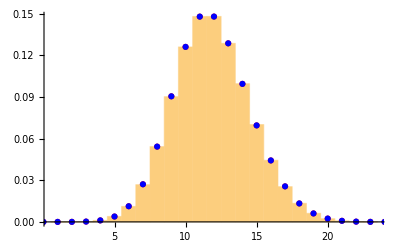

```mathematica
With[{dists=Table[BetaBinomialDistribution[RandomReal[{0,10}],RandomReal[{0,10}],RandomInteger[{1,10}]],5]},
Show[{
Histogram[Total[RandomVariate[#,1000000]&/@dists],{1},"PDF",PlotRange->All],
ListPlot[{
With[{y=Fold[convolvePMF[#1,betaBinomialPMF[#2]]&,betaBinomialPMF[First[dists]],Rest[dists]]},
Transpose[{Range[0,Length[y]-1],y}]
],
With[{y=fourierConvolveBetaBinomials[dists]},
Transpose[{Range[0,Length[y]-1],y}]
]
},
PlotRange->All,PlotStyle->{Red,Blue}
]
}]
]
```

(Both the explicit convolutions and the Fourier method return identical results, so the points lie on top of one another.)

## CVAP estimates

### Common

Get the input data:

```mathematica
acsTracts=KeySort@getACSTracts[Entity["AdministrativeDivision",{"Georgia","UnitedStates"}],Keys[acsCategoriesCodes],$defaultACSVintage];
```

```mathematica
decennialTracts=KeySort@getDecennialTracts[Entity["AdministrativeDivision",{"Georgia","UnitedStates"}],allDecennialVariables,$defaultDecennialVintage];
```

```mathematica
decennialBlocks=getDecennialBlocks[Entity["AdministrativeDivision",{"Georgia","UnitedStates"}],allDecennialVariables];//EchoTiming
```

180.394

```mathematica
(*Export["~/Downloads/decennialBlockData.wxf",decennialBlocks,OverwriteTarget->False]*)
```

~/Downloads/decennialBlockData.wxf

```mathematica
decennialBlocks=Import["~/Downloads/decennialBlockData.wxf"];
```

```mathematica
distributeTractsToBlocks[decennialBlocks_,tractCVAP_,categories_]:=
Association@KeyValueMap[
#1->AssociationMap[
c|->betaBinomialCount[
tractCVAP[geoidTract[#1]][c],
categoryTotal[#2,categories[c]]
],
Keys[categories]
]&,
decennialBlocks
]
```

### CVAP estimates for ACS categories

Compute CVAP for the tracts:

```mathematica
tractCVAPACS=Transpose@AssociationMap[
betaBinomialProportionEstimate[
Values/@acsTracts[[All,{Key[{#,"CVAP"}],Key[{#,"VAP"}]}]]
]&,
Keys[acsCategories]
];//EchoTiming
```

7.41143

Distribute to the blocks:

```mathematica
blockCVAPACS=distributeTractsToBlocks[decennialBlocks,tractCVAPACS,acsCategories];//EchoTiming
```

120.794

```mathematica
blockCVAPACS=;
```

Compute the means of the block-level distributions. (In general, we compute the pmf of the full convolution, but this is a good approximation for development):

```mathematica
blockCVAPACSMeans=Map[betaBinomialMean,blockCVAPACS,{2}];//EchoTiming
```

7.07821

Get the total CVAPs:

```mathematica
Round@Total@blockCVAPACSMeans
```

<|WhiteAlone→4302973,BlackOrAfricanAmericanAlone→2427218,AsianAlone→234087,AmericanIndianAndAlaskaNativeAlone→31931,NativeHawaiianAndOtherPacificIslanderAlone→5171,SomeOtherRaceAlone→209940,TwoOrMore→430106,HispanicOrLatino→442564,WhiteAloneNotHispanicOrLatino→4286246|>

Get district-level CVAPs:

```mathematica
Dataset@districtAggregate[
blockCVAPACSMeans,
Select[blockDistrictPairs,MatchQ[{_,{"13",_}}]]
]
```

### CVAP estimates with litigation VAP and ACS CVAP ratios

This uses citizenship rate data from ACS categories, and blindly applies it to "corresponding" decennial VAP data. This correspondence is somewhat arbitrary:

```mathematica
litigationACSCategories=<|
"LitigationBlack"->"BlackOrAfricanAmericanAlone",
"LitigationHispanic"->"HispanicOrLatino",
"LitigationAsianOrPacificIslander"->"AsianAlone",
"LitigationAmericanIndian"->"AmericanIndianAndAlaskaNativeAlone",
"LitigationSomeOtherRace"->"SomeOtherRaceAlone",
"LitigationWhite"->"WhiteAloneNotHispanicOrLatino"
|>;
```

Compute CVAP for the tracts:

```mathematica
tractCVAPNaive=Transpose@AssociationMap[
betaBinomialProportionEstimate[
Values/@acsTracts[[All,{Key[{litigationACSCategories[#],"CVAP"}],Key[{litigationACSCategories[#],"VAP"}]}]]
]&,
Keys[litigationCategories]
];//EchoTiming
```

4.94552

Distribute to the blocks:

```mathematica
blockCVAPNaive=distributeTractsToBlocks[decennialBlocks,tractCVAPNaive,litigationCategories];//EchoTiming
```

77.501

```mathematica
blockCVAPNaive=;
```

Compute the means of the block-level distributions. (In general, we compute the pmf of the full convolution, but this is a good approximation for development):

```mathematica
blockCVAPNaiveMeans=Map[betaBinomialMean,blockCVAPNaive,{2}];//EchoTiming
```

4.73104

Get the total CVAPs:

```mathematica
Round@Total@blockCVAPNaiveMeans
```

<|LitigationBlack→2543026,LitigationHispanic→409575,LitigationAsianOrPacificIslander→260774,LitigationAmericanIndian→88915,LitigationSomeOtherRace→49276,LitigationWhite→4286246|>

Get district-level CVAPs:

```mathematica
Dataset@districtAggregate[
blockCVAPNaiveMeans,
Select[blockDistrictPairs,MatchQ[{_,{"13",_}}]]
]
```

### With litigation category conversion

```mathematica
betaBinomialCitizenshipRates[tracts_,cats_]:=
Transpose@AssociationMap[
betaBinomialProportionEstimate[
Values/@Round@tracts[[All,{Key[{#,"CVAP"}],Key[{#,"VAP"}]}]]
]&,
cats
]
```

#### V1

```mathematica
litigationTracts1=litigationCategoryEstimate1[acsTracts,decennialTracts];//EchoTiming
```

9.37778

```mathematica
tractCVAPLitigation1=betaBinomialCitizenshipRates[litigationTracts1,Keys[litigationCategories]];//EchoTiming
```

4.77742

```mathematica
blockCVAPLitigation1=distributeTractsToBlocks[decennialBlocks,tractCVAPLitigation1,litigationCategories];//EchoTiming
```

77.7863

```mathematica
blockCVAPLitigation1=;
```

```mathematica
blockCVAPLitigation1Means=Map[betaBinomialMean,blockCVAPLitigation1,{2}];//EchoTiming
```

4.92528

#### V2

```mathematica
litigationTracts2=litigationCategoryEstimate2[acsTracts,decennialTracts];//EchoTiming
```

10.779

```mathematica
tractCVAPLitigation2=betaBinomialCitizenshipRates[litigationTracts2,Keys[litigationCategories]];//EchoTiming
```

4.60266

```mathematica
blockCVAPLitigation2=distributeTractsToBlocks[decennialBlocks,tractCVAPLitigation2,litigationCategories];//EchoTiming
```

77.1708

```mathematica
blockCVAPLitigation2=;
```

```mathematica
blockCVAPLitigation2Means=Map[betaBinomialMean,blockCVAPLitigation2,{2}];//EchoTiming
```

4.68811

#### V3

```mathematica
litigationTracts3=litigationCategoryEstimate3[acsTracts,decennialTracts];//EchoTiming
```

20.0431

```mathematica
tractCVAPLitigation3=betaBinomialCitizenshipRates[litigationTracts3,Keys[litigationCategories]];//EchoTiming
```

4.6955

```mathematica
blockCVAPLitigation3=distributeTractsToBlocks[decennialBlocks,tractCVAPLitigation3,litigationCategories];//EchoTiming
```

78.8069

```mathematica
blockCVAPLitigation3=;
```

```mathematica
blockCVAPLitigation3Means=Map[betaBinomialMean,blockCVAPLitigation3,{2}];//EchoTiming
```

4.70154

### Basic DVAP

This computes CVAP in roughly the way that I think Parker is. The CVAP for each block is computed as the product of decennial VAP with the ACS citizenship rate for the surrounding tract. The the ACS citizenship rate cannot be computed because ACS VAP is 0, then the statewide citizenship rate is used instead.

```mathematica
statewideCitizenshipRate=N@AssociationMap[
c|->Total@acsTracts[[All,Key[{c,"CVAP"}]]]/Total@acsTracts[[All,Key[{c,"VAP"}]]],
Keys[acsCategories]
]
```

<|WhiteAlone→0.957832,BlackOrAfricanAmericanAlone→0.974974,AsianAlone→0.614323,AmericanIndianAndAlaskaNativeAlone→0.761593,NativeHawaiianAndOtherPacificIslanderAlone→0.815686,SomeOtherRaceAlone→0.529674,TwoOrMore→0.844973,HispanicOrLatino→0.581811,WhiteAloneNotHispanicOrLatino→0.986791|>

Get the citizenship rate by category for each tract, replacing tracts with 0 VAP with the statewide rate:

TODO: Maybe do <10 instead of ==0?

```mathematica
tractCitizenshipRate=Map[
tractData|->AssociationMap[
cat|->With[{
vap=tractData[{cat,"VAP"}],
cvap=tractData[{cat,"CVAP"}]
},
If[vap<10,statewideCitizenshipRate[cat],N@cvap/vap]
],
Keys[acsCategories]
],
acsTracts
];
```

```mathematica
blockDVAP=AssociationMap[
block|->AssociationMap[
cat|->tractCitizenshipRate[[geoidTract[block],litigationACSCategories[cat]]]*categoryTotal[decennialBlocks[block],litigationCategories[cat]],
Keys[litigationCategories]
],
Keys[decennialBlocks]
];//EchoTiming
```

73.2789

```mathematica
blockDVAP=;
```

### Parker DVAP

Send from Moon on Slack with this message from Parker:

GA and TX VAP/DVAP: https://www.dropbox.com/scl/fo/a93luzwjamae77yygutsn/AFU0YX_DCZolfdU4PMGlpk8?rlkey=0y3lvskz8l5rej38ov6s5lui2&dl=0
As part of my campaign against bad serialization formats, I’ve chosen to save the outputs as SQLite databases, which can be read like so:
db_url = f"sqlite:///outputs/GA.sqlite3"
block = pd.read_sql_table("block", con=db_url, index_col="GEOID20")
cd_enacted = pd.read_sql_table("cd_enacted", con=db_url, index_col="district")
county = pd.read_sql_table("county", con=db_url, index_col="county")
All data is sourced using the Census API wrappers in gerrytools. I’ve done some basic invariant checks on the processed data.

```mathematica
db=DatabaseReference[FileNameJoin[{NotebookDirectory[],"parkerDVAP","outputs","GA.sqlite3"}]];
```

```mathematica
blockVAPParker=Transpose@<|
"LitigationBlack"->GroupBy[ExternalEvaluate[db->"Rows","SELECT GEOID20, vap_black FROM block;"],First->Last,First],
"LitigationHispanic"->GroupBy[ExternalEvaluate[db->"Rows","SELECT GEOID20, vap_hispanic FROM block;"],First->Last,First],
"LitigationAsianOrPacificIslander"->GroupBy[ExternalEvaluate[db->"Rows","SELECT GEOID20, vap_aapi FROM block;"],First->Last,First],
"LitigationAmericanIndian"->GroupBy[ExternalEvaluate[db->"Rows","SELECT GEOID20, vap_amin FROM block;"],First->Last,First],
"LitigationSomeOtherRace"->GroupBy[ExternalEvaluate[db->"Rows","SELECT GEOID20, vap_other FROM block;"],First->Last,First],
"LitigationWhite"->GroupBy[ExternalEvaluate[db->"Rows","SELECT GEOID20, vap_white FROM block;"],First->Last,First]
|>;
```

```mathematica
blockCVAPParker=Transpose@<|
"LitigationBlack"->GroupBy[ExternalEvaluate[db->"Rows","SELECT GEOID20, dvap_black FROM block;"],First->Last,First],
"LitigationHispanic"->GroupBy[ExternalEvaluate[db->"Rows","SELECT GEOID20, dvap_hispanic FROM block;"],First->Last,First],
"LitigationAsianOrPacificIslander"->GroupBy[ExternalEvaluate[db->"Rows","SELECT GEOID20, dvap_aapi FROM block;"],First->Last,First],
"LitigationAmericanIndian"->GroupBy[ExternalEvaluate[db->"Rows","SELECT GEOID20, dvap_amin FROM block;"],First->Last,First],
"LitigationSomeOtherRace"->GroupBy[ExternalEvaluate[db->"Rows","SELECT GEOID20, dvap_other FROM block;"],First->Last,First],
"LitigationWhite"->GroupBy[ExternalEvaluate[db->"Rows","SELECT GEOID20, dvap_white FROM block;"],First->Last,First]
|>;
```

```mathematica
blockCVAPParker=;
```

VAP numbers match exactly:

```mathematica
KeySort@blockVAPParker===(t|->categoryTotal[t,#]&/@litigationCategories)/@KeySort@decennialBlocks
```

True

```mathematica
Dataset[Transpose@<|
"Parker VAP"->Total@blockVAPParker,
"Decennial VAP"->(categoryTotal[Total@decennialTracts,#]&/@litigationCategories)
|>]
```

### Comparison

Everything is computed with 2020 vintages of both decennial Census and ACS. (Except the data from Parker, where I'm not sure about the ACS vintage.)

Parker CVAP: From Parker's files.

Basic CVAP: Constructed in roughly the same way as I think Parker's was constructed.

Basic beta-binomial CVAP: Same as basic CVAP but uses beta-binomial estimation to get citizenship rates (instead of replacing 0s with the statewide rate).

Litigation CVAP 1: Category conversion using the first of the formulas given above. Beta-binomial estimation used to distribute to blocks.

```mathematica
Dataset[Transpose@<|
"Parker DVAP"->Round@Total@blockCVAPParker,
"Reconstructed DVAP"->Round@Total@blockDVAP,
"Basic beta-binomial CVAP"->Round@Total@blockCVAPNaiveMeans,
"Litigation CVAP V1"->Round@Total@blockCVAPLitigation1Means,
"Litigation CVAP V2"->Round@Total@blockCVAPLitigation2Means,
"Litigation CVAP V3"->Round@Total@blockCVAPLitigation3Means
|>]
```

```mathematica
stateDistrictPairs=Select[blockDistrictPairs,MatchQ[{_,{"13",_}}]];
```

```mathematica
Dataset[Transpose@<|
"Parker DVAP"->Round@districtAggregate[blockCVAPParker,stateDistrictPairs],
"Reconstructed DVAP"->Round@districtAggregate[blockDVAP,stateDistrictPairs],
"Basic beta-binomial CVAP"->Round@districtAggregate[blockCVAPNaiveMeans,stateDistrictPairs],
"Litigation CVAP V1"->Round@districtAggregate[blockCVAPLitigation1Means,stateDistrictPairs],
"Litigation CVAP V2"->Round@districtAggregate[blockCVAPLitigation2Means,stateDistrictPairs],
"Litigation CVAP V3"->Round@districtAggregate[blockCVAPLitigation3Means,stateDistrictPairs]
|>]
```

### Exporting to CSVs

```mathematica
csvDirectory=FileNameJoin[{NotebookDirectory[],"csvOutput"}]
```

/Users/christopher/Library/CloudStorage/Dropbox/UChicago/voterfileData/moonDuchin/cvapEstimation/csvOutput

#### Block-level

```mathematica
exportBlockCSV[path_,blocks_]:=
Export[
path,
Prepend[
KeyValueMap[Prepend[#2,#1]&,Values/@blocks],
Prepend[Keys[First[blocks]],"GEOID2020"]
]
]
```

```mathematica
exportBlockCSV[FileNameJoin[{csvDirectory,"blocks","parkerDVAP.csv"}],KeySort@Round@blockCVAPParker]
```

/Users/christopher/Library/CloudStorage/Dropbox/UChicago/voterfileData/moonDuchin/cvapEstimation/csvOutput/blocks/parkerDVAP.csv

```mathematica
exportBlockCSV[FileNameJoin[{csvDirectory,"blocks","reconstructedDVAP.csv"}],KeySort@Round@blockDVAP]
```

/Users/christopher/Library/CloudStorage/Dropbox/UChicago/voterfileData/moonDuchin/cvapEstimation/csvOutput/blocks/reconstructedDVAP.csv

```mathematica
exportBlockCSV[FileNameJoin[{csvDirectory,"blocks","betaBinomialNaiveCVAP.csv"}],KeySort@Round@blockCVAPNaiveMeans]
```

/Users/christopher/Library/CloudStorage/Dropbox/UChicago/voterfileData/moonDuchin/cvapEstimation/csvOutput/blocks/betaBinomialNaiveCVAP.csv

```mathematica
exportBlockCSV[FileNameJoin[{csvDirectory,"blocks","betaBinomialLitigationCVAP1.csv"}],KeySort@Round@blockCVAPLitigation1Means]
```

/Users/christopher/Library/CloudStorage/Dropbox/UChicago/voterfileData/moonDuchin/cvapEstimation/csvOutput/blocks/betaBinomialLitigationCVAP1.csv

```mathematica
exportBlockCSV[FileNameJoin[{csvDirectory,"blocks","betaBinomialLitigationCVAP2.csv"}],KeySort@Round@blockCVAPLitigation2Means]
```

/Users/christopher/Library/CloudStorage/Dropbox/UChicago/voterfileData/moonDuchin/cvapEstimation/csvOutput/blocks/betaBinomialLitigationCVAP2.csv

```mathematica
exportBlockCSV[FileNameJoin[{csvDirectory,"blocks","betaBinomialLitigationCVAP3.csv"}],KeySort@Round@blockCVAPLitigation3Means]
```

/Users/christopher/Library/CloudStorage/Dropbox/UChicago/voterfileData/moonDuchin/cvapEstimation/csvOutput/blocks/betaBinomialLitigationCVAP3.csv

#### District-level

```mathematica
exportDistrictCSV[path_,districts_]:=
Export[
path,
Prepend[
KeyValueMap[Prepend[#2,#1]&,Values/@districts],
Prepend[Keys[First[districts]],"District"]
]
]
```

```mathematica
exportDistrictCSV[FileNameJoin[{csvDirectory,"districts","parkerDVAP.csv"}],KeySort@KeyMap[Last]@Round@districtAggregate[blockCVAPParker,stateDistrictPairs]]
```

/Users/christopher/Library/CloudStorage/Dropbox/UChicago/voterfileData/moonDuchin/cvapEstimation/csvOutput/districts/parkerDVAP.csv

```mathematica
exportDistrictCSV[FileNameJoin[{csvDirectory,"districts","reconstructedDVAP.csv"}],KeySort@KeyMap[Last]@Round@districtAggregate[blockDVAP,stateDistrictPairs]]
```

/Users/christopher/Library/CloudStorage/Dropbox/UChicago/voterfileData/moonDuchin/cvapEstimation/csvOutput/districts/reconstructedDVAP.csv

```mathematica
exportDistrictCSV[FileNameJoin[{csvDirectory,"districts","betaBinomialNaiveCVAP.csv"}],KeySort@KeyMap[Last]@Round@districtAggregate[blockCVAPNaiveMeans,stateDistrictPairs]]
```

/Users/christopher/Library/CloudStorage/Dropbox/UChicago/voterfileData/moonDuchin/cvapEstimation/csvOutput/districts/betaBinomialNaiveCVAP.csv

```mathematica
exportDistrictCSV[FileNameJoin[{csvDirectory,"districts","betaBinomialLitigationCVAP1.csv"}],KeySort@KeyMap[Last]@Round@districtAggregate[blockCVAPLitigation1Means,stateDistrictPairs]]
```

/Users/christopher/Library/CloudStorage/Dropbox/UChicago/voterfileData/moonDuchin/cvapEstimation/csvOutput/districts/betaBinomialLitigationCVAP1.csv

```mathematica
exportDistrictCSV[FileNameJoin[{csvDirectory,"districts","betaBinomialLitigationCVAP2.csv"}],KeySort@KeyMap[Last]@Round@districtAggregate[blockCVAPLitigation2Means,stateDistrictPairs]]
```

/Users/christopher/Library/CloudStorage/Dropbox/UChicago/voterfileData/moonDuchin/cvapEstimation/csvOutput/districts/betaBinomialLitigationCVAP2.csv

```mathematica
exportDistrictCSV[FileNameJoin[{csvDirectory,"districts","betaBinomialLitigationCVAP3.csv"}],KeySort@KeyMap[Last]@Round@districtAggregate[blockCVAPLitigation3Means,stateDistrictPairs]]
```

/Users/christopher/Library/CloudStorage/Dropbox/UChicago/voterfileData/moonDuchin/cvapEstimation/csvOutput/districts/betaBinomialLitigationCVAP3.csv

### Why is the total CVAP for SomeOtherRace lower in Litigation V3 than either of the other Litigation versions?

See here:

```mathematica
Dataset[Transpose@<|
"Litigation CVAP V1"->Round@Total@blockCVAPLitigation1Means,
"Litigation CVAP V2"->Round@Total@blockCVAPLitigation2Means,
"Litigation CVAP V3"->Round@Total@blockCVAPLitigation3Means
|>]
```

The overall citizenship rate is intermediate according to the tract-level estimates:

```mathematica
Round@Total[litigationTracts1][{"LitigationSomeOtherRace","CVAP"}]/Round@Total[litigationTracts1][{"LitigationSomeOtherRace","VAP"}]//N
```

0.745715

```mathematica
Round@Total[litigationTracts2][{"LitigationSomeOtherRace","CVAP"}]/Round@Total[litigationTracts2][{"LitigationSomeOtherRace","VAP"}]//N
```

0.648099

```mathematica
Round@Total[litigationTracts3][{"LitigationSomeOtherRace","CVAP"}]/Round@Total[litigationTracts3][{"LitigationSomeOtherRace","VAP"}]//N
```

0.688964

But after running MLE, the mean is lowest for the prior distribution with Litigation V3:

```mathematica
mleDistribution@proportionsMLE[Values/@Round@litigationTracts1[[All,{Key[{"LitigationSomeOtherRace","CVAP"}],Key[{"LitigationSomeOtherRace","VAP"}]}]]]
```

BetaDistribution[1.27681,0.308099]

```mathematica
Mean[BetaDistribution[1.276811426281039,0.3080993333709014]]
```

0.805605

```mathematica
mleDistribution@proportionsMLE[Values/@Round@litigationTracts2[[All,{Key[{"LitigationSomeOtherRace","CVAP"}],Key[{"LitigationSomeOtherRace","VAP"}]}]]]
```

BetaDistribution[0.651933,0.113637]

```mathematica
Mean[BetaDistribution[0.6519329262359816,0.11363656041316984]]
```

0.851566

```mathematica
mleDistribution@proportionsMLE[Values/@Round@litigationTracts3[[All,{Key[{"LitigationSomeOtherRace","CVAP"}],Key[{"LitigationSomeOtherRace","VAP"}]}]]]
```

BetaDistribution[0.983268,0.262029]

```mathematica
Mean[BetaDistribution[0.9832683997594077,0.2620292583296086]]
```

0.789585

### Gibbs sampler

#### Slice sampling

From Radford. M. Neal article:
https://projecteuclid.org/journalArticle/Download?urlId=10.1214%2Faos%2F1056562461

```mathematica
steppingOut[g_,x0_,z_,w_,m_]:=
Module[{u,l,r,v,j,k},
u=RandomReal[];
l=x0-w*u;
r=l+w;
v=RandomReal[];
j=Floor[m*v];
k=m-1-j;
While[j>0&&z<g[l],
l=l-w;
j=j-1
];
While[k>0&&z<g[r],
r=r+w;
k=k-1
];
{l,r}
]
```

```mathematica
shrinkage[g_,x0_,z_,{l_,r_}]:=
Module[{l1,r1,u,x1},
{l1,r1}={l,r};
While[True,
u=RandomReal[];
x1=l1+u*(r1-l1);
Which[
z<g[x1],Return[x1],
x1<x0,l1=x1,
True,r1=x1
]
]
]
```

```mathematica
sliceStep[g_,x0_,w_,m_,{l0_,r0_}]:=
Module[{z,l,r},
z=g[x0]-RandomVariate[ExponentialDistribution[1]];
If[l0===Automatic||r0===Automatic,
{l,r}=steppingOut[g,x0,z,w,m];
If[l0=!=Automatic,l=l0];
If[r0=!=Automatic,r=r0]
,
{l,r}={l0,r0}
];
shrinkage[g,x0,z,{l,r}]
]
sliceStep[g_,x0_,w_,m_]:=sliceStep[g,x0,w,m,{Automatic,Automatic}]
```

#### Implementation

α\[Distributed]Gamma(1/2,1/2)
β\[Distributed]Gamma(1/2,1/2)
p_t\[Distributed]Beta(α,β)
VAP_t\[Distributed]π(·)
CVAP_t\[Distributed]Binomial(VAP_t,p_t)
OverTilde[VAP_t]\[Distributed]Normal(VAP_t,VAPError_t)
OverTilde[CVAP_t]\[Distributed]Normal(CVAP_t,CVAPError_t)

CVAP_b\[Distributed]Binomial(VAP_b,p_t_b)

Sampling:
α: Slice sampling
β: Slice sampling
p_t: Conjugacy
VAP_t: ???
CVAP_t: Discrete enumeration

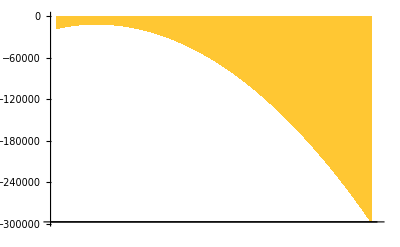

```mathematica
With[{n=3000,p=0.99,x=Range[0,3000]},
BarChart[logPDF[BinomialDistribution[n,p],x]+logPDF[NormalDistribution[300.,3.5],x]]
]
```

```mathematica
logPDF[BinomialDistribution[n_,p_],x_]:=(n-x) Log[1-p]+x Log[p]+Log[Binomial[n,x]]
logPDF[NormalDistribution[μ_,σ_],x_]:=-(x-μ)^2/(2 σ^2)+1/2 (-Log[2]-Log[π])-Log[σ]
```

```mathematica
Module[(*{n=100,x,μ=3.4,σ=1.3,p=0.99,normalCDF,normalPDF,binomialPDF}*){n=3000,x,μ=300.0,σ=3.5,p=0.99,normalCDF,normalPDF,binomialPDF},
x=Range[0,n+1];

(*normalCDF=CDF[NormalDistribution[μ,σ],x];
normalPDF=Log[Rest[normalCDF]-Most[normalCDF]];*)
normalPDF=Log[1/2 Erf[(μ-Range[1,n+1])/(√2 σ),(μ-Range[0,n])/(√2 σ)]];
binomialPDF=logPDF[BinomialDistribution[n,p],Range[0,n]];
Echo[Exp[normalPDF+binomialPDF]];

(*normalPDF=Rest[normalCDF]-Most[normalCDF];*)
x=Range[0,n];
normalPDF=1/2 Erf[(μ-(x+1))/(√2 σ),(μ-x)/(√2 σ)];
binomialPDF=PDF[BinomialDistribution[n,p],Range[0,n]];
Echo[Normalize[normalPDF*binomialPDF,Total]];
BarChart[Normalize[normalPDF*binomialPDF,Total]]
]
```

General::munfl: Exp[-3653.12] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3677.57] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3628.75] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
logBetaPDF[α_,β_,xs_]:=(α-1)*Total[Log[xs]]+(β-1)*Total[Log[1-xs]]-Length[xs]*logBeta[α,β]
```

```mathematica
αPrior[]:=GammaDistribution[1,1]
αInit[]:=<|"α"->RandomVariate@αPrior[]|>
αUpdate[s_]:=
Module[{α,logLikelihood,v},
(*TODO: This Clip is wrong!*)
logLikelihood=logBetaPDF[α,s["β"],Clip[Values@s["p"],{100*$MachineEpsilon,1.-100*$MachineEpsilon}]]+LogLikelihood[αPrior[],{α}];
(*v=sliceStep[logLikelihood/.α->#&,s["α"],1.,20,{0.,Automatic}];*)
v=Nest[sliceStep[logLikelihood/.α->#&,#,1.,20,{0.,Automatic}]&,s["α"],10];
<|"α"->v|>
]
```

```mathematica
βPrior[]:=GammaDistribution[1,1]
βInit[]:=<|"β"->RandomVariate@βPrior[]|>
βUpdate[s_]:=
Module[{β,logLikelihood,v},
(*TODO: This Clip is wrong!*)
logLikelihood=logBetaPDF[s["α"],β,Clip[Values@s["p"],{100*$MachineEpsilon,1.-100*$MachineEpsilon}]]+LogLikelihood[βPrior[],{β}];
(*v=sliceStep[logLikelihood/.β->#&,s["β"],1.,20,{0.,Automatic}];*)
v=Nest[sliceStep[logLikelihood/.β->#&,#,1.,20,{0.,Automatic}]&,s["β"],10];
<|"β"->v|>
]
```

```mathematica
pPrior[s_]:=BetaDistribution[s["α"],s["β"]]
pInit[s_]:=<|"p"->AssociationMap[RandomVariate@pPrior[s]&,Keys@s["tractCVAP"]]|>
pUpdate[s_]:=
Module[{αs,βs},
αs=s["α"]+s["tractCVAP"];
βs=s["β"]+s["tractVAP"]-s["tractCVAP"];
(*TODO: Do we need to take the block-level data into account?*)
<|"p"->MapThread[RandomVariate@BetaDistribution[#1,#2]&,{αs,βs}]|>
]
```

This initialization is wrong:

```mathematica
tractVAPInit[]:=<|"tractVAP"->acsTracts[[All,Key[{"HispanicOrLatino","VAP"}]]]|>
tractCVAPInit[]:=<|"tractCVAP"->acsTracts[[All,Key[{"HispanicOrLatino","CVAP"}]]]|>
```

The margins of error are massive.

```mathematica
(*tractVAPUpdate[s_]:=<||>
tractCVAPUpdate[s_]:=<||>*)
```

```mathematica
logPDF[BinomialDistribution[n,p],x]+logPDF[NormalDistribution[300.,3.5],x]
```

```mathematica
tractVAPUpdate[s_]:=
Module[{c="HispanicOrLatino",se=1.645,out},
out=AssociationMap[
Clip[
Round@RandomVariate[NormalDistribution[
acsTracts[[#,Key[{"HispanicOrLatino","VAP"}]]],
acsTracts[[#,Key[{"HispanicOrLatino","VAPError"}]]]/se
]],
{s[["tractCVAP",#]],Infinity}
]&,
Keys[acsTracts]
];
<|"tractVAP"->out|>
]
```

```mathematica
tractCVAPUpdate[s_]:=
Module[{c="HispanicOrLatino",se=1.645,out},
out=AssociationMap[
Clip[
Round@RandomVariate[NormalDistribution[
acsTracts[[#,Key[{"HispanicOrLatino","CVAP"}]]],
acsTracts[[#,Key[{"HispanicOrLatino","CVAPError"}]]]/se
]],
{0,s[["tractVAP",#]]}
]&,
Keys[acsTracts]
];
<|"tractCVAP"->out|>
]
```

```mathematica
initLatents[]:=
Module[{s},
s=<||>;
s//=Append@tractVAPInit[];
s//=Append@tractCVAPInit[];
s//=Append@αInit[];
s//=Append@βInit[];
s//=Append@pInit[s];
s
]
```

```mathematica
updateLatents[s0_]:=
Module[{s=s0},
s//=Append@tractVAPUpdate[s];
s//=Append@tractCVAPUpdate[s];
s//=Append@pUpdate[s];
s//=Append@αUpdate[s];
s//=Append@βUpdate[s];
s
]
```

```mathematica
chains=Table[Module[{s},
s=initLatents[];
NestList[updateLatents,s,1000]
]//EchoTiming,4];
```

35.2389

34.8152

35.2864

34.76

```mathematica
Beep[]
```

```mathematica
samples=Catenate@chains[[All,100;;]];
```

```mathematica
N@tractCVAP["13001950100"]/tractVAP["13001950100"]
```

0.575581

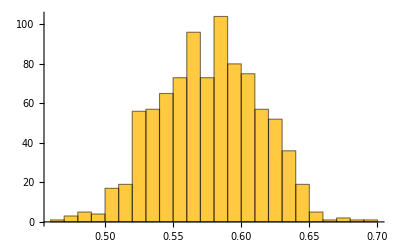

```mathematica
Histogram@samples[[All,"p","13001950100"]]
```

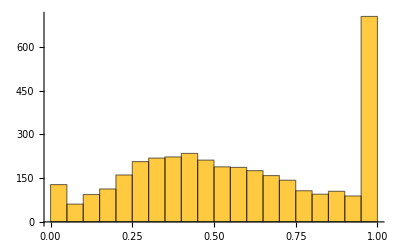

```mathematica
Histogram[samples[[All,"p","13001950100"]],25]
```

```mathematica
ReverseSort[tractVAP][[;;10]]
```

<|13313000401→3385,13139001101→3008,13139001102→2680,13139001202→2668,13313001200→2504,13313001300→2347,13135050440→2155,13135050539→2093,13139001404→2080,13139000702→2074|>

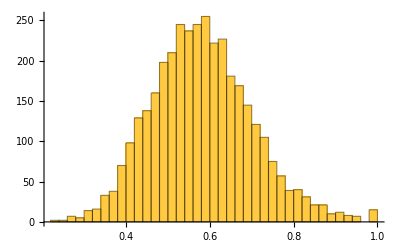

```mathematica
Histogram[samples[[All,"p","13313000401"]],50]
```

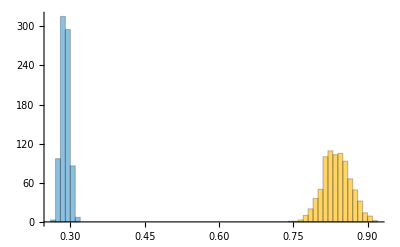

```mathematica
Histogram[{samples[[All,"α"]],samples[[All,"β"]]},{0.01}]
```

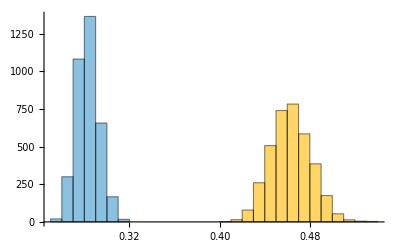

```mathematica
Histogram[{samples[[All,"α"]],samples[[All,"β"]]},{0.01}]
```

```mathematica
N@Total[tractCVAP]/Total[tractVAP]
```

0.616492

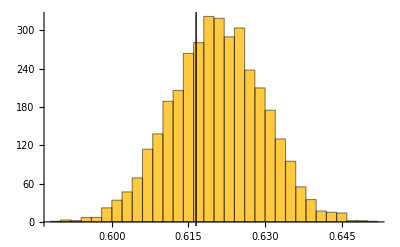

```mathematica
Histogram[Mean@BetaDistribution[#α,#β]&/@samples,Epilog->InfiniteLine[{N@Total[tractCVAP]/Total[tractVAP],0},{0,1}]]
```

```mathematica
Total@acsTracts[[All,Key[{"HispanicOrLatino","VAP"}]]]
```

702322

```mathematica
Sqrt@Total[acsTracts[[All,Key[{"HispanicOrLatino","VAPError"}]]]^2]
```

9003.1

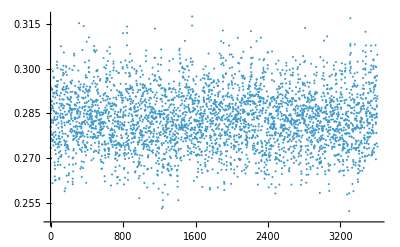

```mathematica
ListPlot@samples[[All,"β"]]
```

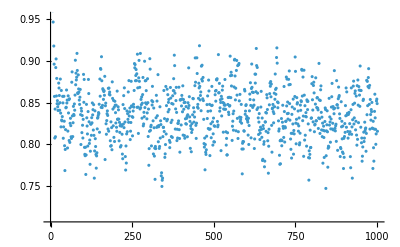

```mathematica
ListPlot@samples[[All,"α"]]
```

```mathematica
tractVAP=acsTracts[[All,Key[{"HispanicOrLatino","VAP"}]]];
tractCVAP=acsTracts[[All,Key[{"HispanicOrLatino","CVAP"}]]];
```

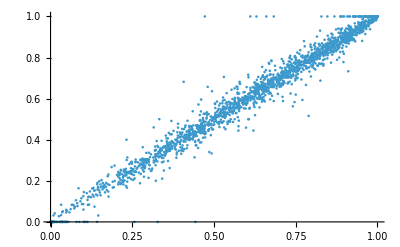

```mathematica
ListPlot@Values@Merge[{
samples[[-1,"p"]],
Quiet[N@tractCVAP/tractVAP]
},Identity]
```

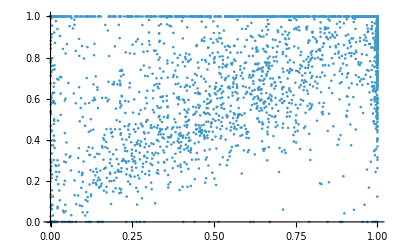

```mathematica
ListPlot@Values@Merge[{
samples[[-1,"p"]],
Quiet[N@tractCVAP/tractVAP]
},Identity]
```

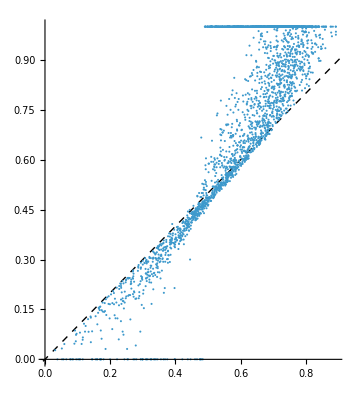

```mathematica
ListPlot[
Values@Merge[{
Mean@samples[[All,"p"]],
Quiet[N@tractCVAP/tractVAP]
},Identity],
AspectRatio->Automatic,
Epilog->{Dashed,InfiniteLine[{0,0},{1,1}]}
]
```

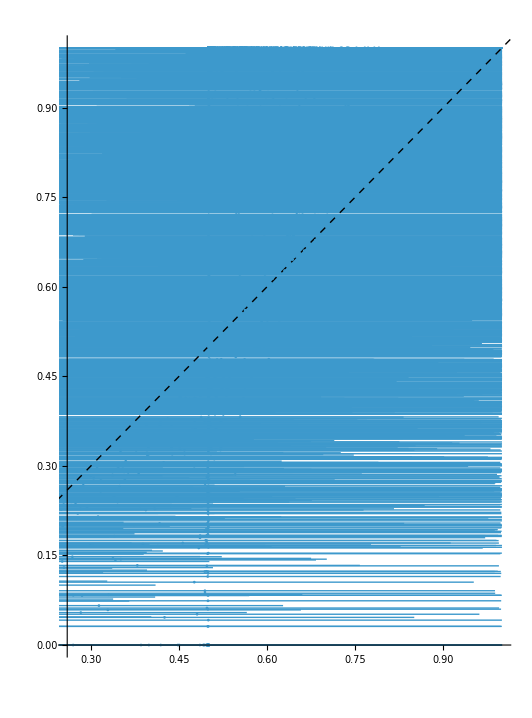

```mathematica
ListPlot[
Values@Merge[{
AssociationThread[
Keys@samples[[1,"p"]],
Interval@Quantile[#,{0.025,0.975}]&/@Transpose[Values/@samples[[All,"p"]]]
],
Quiet[N@tractCVAP/tractVAP]
},Identity],
AspectRatio->Automatic,
Epilog->{Dashed,InfiniteLine[{0,0},{1,1}]}
]
```

MLE estimate:

```mathematica
Module[{r,c},
{r,c}=proportionsMLE[Values@Merge[{tractCVAP,tractVAP},Identity]];
BetaDistribution[r*c,(1-r)*c]
]
```

BetaDistribution[1.03815,0.312908]

```mathematica
Solve[r*c==(1-r)*c==1/2,{r,c}]
```

{{r→1/2,c→1}}

```mathematica
(Gamma[α+β]^k p^α q^β)/(Gamma[α]^k Gamma[β]^k)
```

```mathematica
betaPriorPDF[α_,β_,p_,q_,k_]:=(Gamma[α+β]^k p^α q^β)/(Gamma[α]^k Gamma[β]^k)
```

```mathematica
logBetaPriorPDF[α_,β_,p_,q_,k_]:=Piecewise[{{α Log[p]+β Log[q]-k LogGamma[α]-k LogGamma[β]+k LogGamma[α+β],α>0&&β>0}}]
```

```mathematica
PowerExpand@Log[(Gamma[α+β]^k p^α q^β)/(Gamma[α]^k Gamma[β]^k)]
```

α Log[p]+β Log[q]-k Log[Gamma[α]]-k Log[Gamma[β]]+k Log[Gamma[α+β]]

```mathematica
FullSimplify@D[(Gamma[α+β]^k p^α q^β)/(Gamma[α]^k Gamma[β]^k),α]
```

p^α q^β Gamma[α]^-k Gamma[β]^-k Gamma[α+β]^k (Log[p]-k PolyGamma[0,α]+k PolyGamma[0,α+β])

```mathematica
betaPriorPDF[α,0.5,0.4,0.7,10]
```

(0.00273401 0.4^α Gamma[0.5+α]^10)/Gamma[α]^10

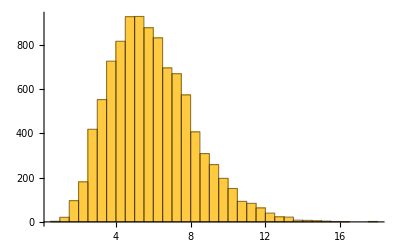

```mathematica
Histogram@NestList[x|->sliceStep[logBetaPriorPDF[#,0.5,0.4,0.7,10]&,x,1.,10,{0.,Automatic}],0.5,10000]
```

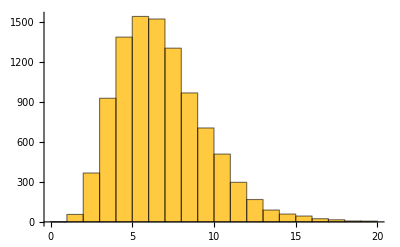

```mathematica
Histogram@Table[Nest[x|->sliceStepBounded[logBetaPriorPDF[#,0.5,0.4,0.7,10]&,x,{0.,20.}],0.5,10],10000]
```

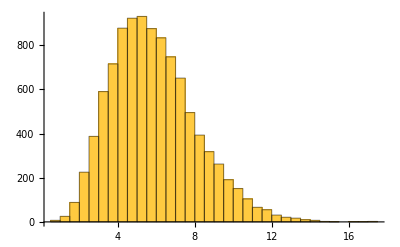

```mathematica
Histogram@Table[Nest[x|->sliceStep[logBetaPriorPDF[#,0.5,0.4,0.7,10]&,x,1.,10,{0.,Automatic}],0.5,10],10000]
```

```mathematica
NestList[x|->sliceStep[betaPriorPDF[#,0.5,0.4,0.7,10]&,x,1.,10],0.5,10]
```

{0.5,-5.39785,-5.5775,-5.44696,-5.52592,-5.475,-5.50752,-5.50585,-5.49448,-5.49717,-5.5027}

```mathematica
Reduce[betaPriorPDF[α,0.5,0.4,0.7,10]==y,α,Reals]
```

Reduce::inex: Reduce was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Reduce require exact input, providing Reduce with an exact version of the system may help.

Reduce[(0.00273401 0.4^α Gamma[0.5+α]^10)/Gamma[α]^10==y,α,ℝ]

```mathematica
RepeatedTiming[RandomVariate@ProbabilityDistribution[betaPriorPDF[α,0.5,0.4,0.7,10],{α,0,Infinity},Method->"Normalize"],5]
```

{0.506191,4.92908}

```mathematica
Integrate[(Gamma[α+β]^k p^α q^β)/(Gamma[α]^k Gamma[β]^k),{α,0,Infinity}]
```

$Aborted

```mathematica
ProbabilityDistribution[(Gamma[α+β]^k p^α q^β)/(Gamma[α]^k Gamma[β]^k),{α,0,Infinity},Method->"Normalize"]
```

ProbabilityDistribution[(p^(x+β) Gamma[x]^-k Gamma[β]^-k Gamma[x+β]^k)/(∫_0^∞ p^(x+β) Gamma[x]^-k Gamma[β]^-k Gamma[x+β]^kⅆx),{x,0,∞}]

```mathematica
%407/.p
```

ProbabilityDistribution[(p^(x+β) Gamma[x]^-k Gamma[β]^-k Gamma[x+β]^k)/(∫_0^∞ p^(x+β) Gamma[x]^-k Gamma[β]^-k Gamma[x+β]^kⅆx),{x,0,∞}]

```mathematica
aPrior[]
```

```mathematica
pPrior[]:=BetaDistribution[]
```

## Margins of error

### Correlated errors

Request data from Georgia:

```mathematica
apiOut=censusQuery[
{"data",ToString[$defaultACSVintage],"acs","acs5"},
{
"get"->StringRiffle[Union[getVAPVarsACS["HispanicOrLatino"],getVAPErrorVarsACS["HispanicOrLatino"]],","],
"for"->"tract:*",
"in"->"state:"<>Replace[Entity["AdministrativeDivision",{"Georgia","UnitedStates"}],state_Entity:>state["FIPSCode"]],
"in"->"county:*"
}
];
```

```mathematica
getVAPVarsACS["HispanicOrLatino"]
```

{B05003I_008E,B05003I_019E}

The total number of voting-age Hispanic or Latino males exactly matches the state-level data:

```mathematica
Total@ToExpression@apiOut[[All,"B05003I_008E"]]
```

369156

However, aggregating the margins of error gives a much larger margin of error than the state-level one, which is ±1010:

```mathematica
Sqrt@N@Total[ToExpression[apiOut[[All,"B05003I_008M"]]]^2]
```

6735.15

### Margins of error are huge

The margins of error are massive.

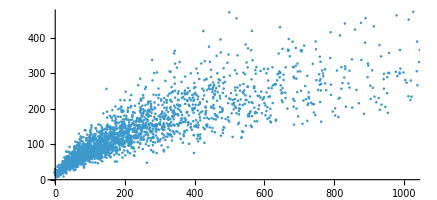

```mathematica
ListPlot[
Values@Merge[{
acsTracts[[All,Key[{"HispanicOrLatino","VAP"}]]],
acsTracts[[All,Key[{"HispanicOrLatino","VAPError"}]]]
},Identity],
AspectRatio->Automatic
]
```

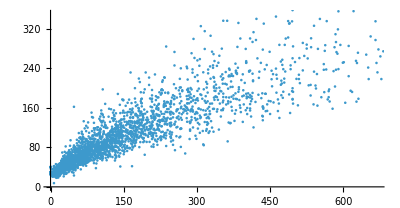

```mathematica
ListPlot[
Values@Merge[{
acsTracts[[All,Key[{"HispanicOrLatino","CVAP"}]]],
acsTracts[[All,Key[{"HispanicOrLatino","CVAPError"}]]]
},Identity],
AspectRatio->Automatic
]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

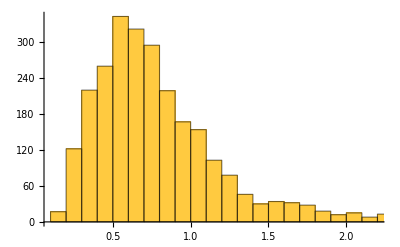

```mathematica
Histogram@Values@Merge[{
acsTracts[[All,Key[{"HispanicOrLatino","VAP"}]]],
acsTracts[[All,Key[{"HispanicOrLatino","VAPError"}]]]
},#[[2]]/#[[1]]&]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

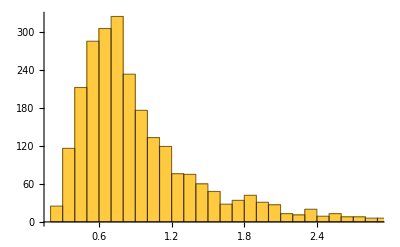

```mathematica
Histogram@Values@Merge[{
acsTracts[[All,Key[{"HispanicOrLatino","CVAP"}]]],
acsTracts[[All,Key[{"HispanicOrLatino","CVAPError"}]]]
},#[[2]]/#[[1]]&]
```

```mathematica
vapError=Merge[{
acsTracts[[All,Key[{"HispanicOrLatino","VAP"}]]],
acsTracts[[All,Key[{"HispanicOrLatino","VAPError"}]]]
},Apply[Around[#1,#2]&]
];
cvapError=Merge[{
acsTracts[[All,Key[{"HispanicOrLatino","CVAP"}]]],
acsTracts[[All,Key[{"HispanicOrLatino","CVAPError"}]]]
},Apply[Around[#1,#2]&]
];
```

```mathematica
Merge[{cvapError,vapError},Apply[#1/#2&]]
```

Power::infy: Infinite expression 1/0.^2 encountered.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
sampleVAP[cvap_,vapEstimate_,vapError_]:=
Round@RandomVariate@TruncatedDistribution[{cvap,Infinity},NormalDistribution[vapEstimate,vapError]]
sampleCVAP[vap_,cvapEstimate_,cvapError_]:=
If[vap==0,0,Round@RandomVariate@TruncatedDistribution[{0,vap},NormalDistribution[cvapEstimate,cvapError]]]
```

```mathematica
chains=Module[{tract=Keys[acsTracts][[1]],vapEstimate,vapError,cvapEstimate,cvapError,vap,cvap},
vapEstimate=acsTracts[[tract,Key[{"HispanicOrLatino","VAP"}]]];
vapError=acsTracts[[tract,Key[{"HispanicOrLatino","VAPError"}]]];
cvapEstimate=acsTracts[[tract,Key[{"HispanicOrLatino","CVAP"}]]];
cvapError=acsTracts[[tract,Key[{"HispanicOrLatino","CVAPError"}]]];

vap=sampleVAP[0,vapEstimate,vapError];
cvap=sampleCVAP[vap,cvapEstimate,cvapError];
Table[
Table[
vap=sampleVAP[cvap,vapEstimate,vapError];
cvap=sampleCVAP[vap,cvapEstimate,cvapError];
{cvap,vap},
{i,10000}
],
1
]
];//EchoTiming
```

2.07138

```mathematica
samples=Catenate@chains[[All,1000;;]];
```

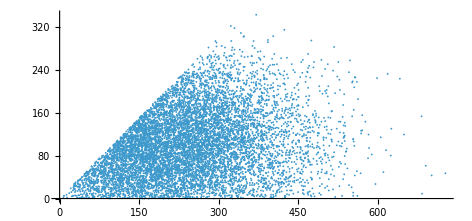

```mathematica
ListPlot[Reverse/@samples,AspectRatio->Automatic]
```

This is hopelessly high variance:

Divide::indet: Indeterminate expression 0./0. encountered.

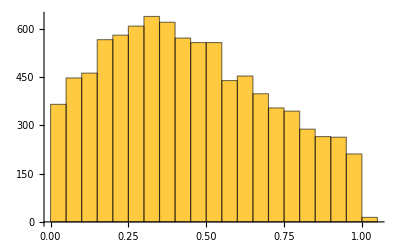

```mathematica
Histogram[Divide@@@N@samples]
```

### Variance replicates

The best way to estimate the MoE for a combination of ACS variables is using variance replicate tables, which can be used to estimate margins of error in the same way that the MoEs are computed in the API tables.

#### Getting replicate tables

```mathematica
varianceReplicateRequest[var_,state_,vintage_:$defaultACSVintage]:=
HTTPRequest[<|
"Scheme"->"https",
"Domain"->"www2.census.gov",
"Path"->{"programs-surveys","acs","replicate_estimates",vintage,"data","5-year","140",var<>"_"<>Replace[state,_Entity:>state["FIPSCode"]]<>".csv.zip"}
|>]
```

```mathematica
varianceReplicateTableRaw[var_,state_,vintage_:$defaultACSVintage]:=
Enclose@Module[{resp},
resp=Confirm@URLRead@varianceReplicateRequest[var,state,vintage];
Import[resp,{"ZIP",StringTemplate["140/``_``.csv"][var,Replace[state,_Entity:>state["FIPSCode"]]],"Tabular"}]
]
```

```mathematica
varianceReplicateTable[var_,state_,vintage_:$defaultACSVintage]:=
Enclose@Module[{tab},
tab=Confirm@varianceReplicateTableRaw[var,state,vintage];
tab=Select[tab,!MissingQ[#GEOID]&];
ConstructColumns[tab,{
"GEOID"->Function[StringDrop[#GEOID,9]],
"Order"->Function[#ORDER],
"Estimate"->Function[#ESTIMATE],
"VarianceReplicates"->Lookup[Table["Var_Rep"<>ToString[i],{i,80}]]
}]
]
```

```mathematica
tab=varianceReplicateTable["B05003",Entity["AdministrativeDivision",{"Georgia","UnitedStates"}]];
```

```mathematica
vap=GroupBy[Normal@Select[tab,#Order===8||#Order===19&],Lookup["GEOID"]->KeyTake[{"Estimate","VarianceReplicates"}],Total];
```

```mathematica
cvap=GroupBy[Normal@Select[tab,#Order===9||#Order===11||#Order===20||#Order===22&],Lookup["GEOID"]->KeyTake[{"Estimate","VarianceReplicates"}],Total];
```

#### VAP and CVAP variance replicates are correlated

VAP and CVAP variance replicates are correlated:

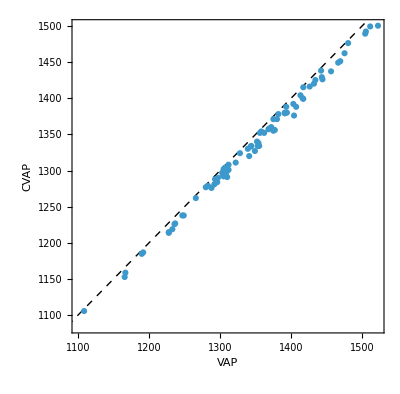

```mathematica
ListPlot[
Transpose@{
vap[[5,"VarianceReplicates"]],
cvap[[5,"VarianceReplicates"]]
},
AspectRatio->Automatic,
Epilog->{Dashed,InfiniteLine[{0,0},{1,1}]},
Frame->True,
FrameLabel->{"VAP","CVAP"}
]
```

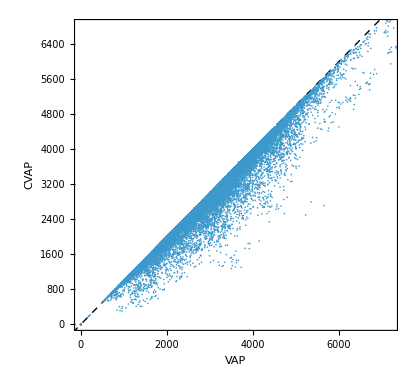

```mathematica
ListPlot[
RandomSample[Transpose@{
Flatten@Values@vap[[All,"VarianceReplicates"]],
Flatten@Values@cvap[[All,"VarianceReplicates"]]
},20000],
AspectRatio->Automatic,
Epilog->{Dashed,InfiniteLine[{0,0},{1,1}]},
Frame->True,
FrameLabel->{"VAP","CVAP"}
]
```

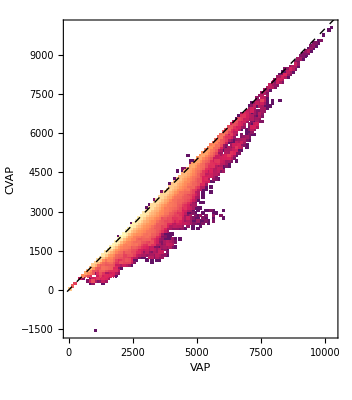

```mathematica
DensityHistogram[
Transpose@{
Flatten@Values@vap[[All,"VarianceReplicates"]],
Flatten@Values@cvap[[All,"VarianceReplicates"]]
},
{{100},{100}},
{"Log","Count"},
AspectRatio->Automatic,
Epilog->{Dashed,InfiniteLine[{0,0},{1,1}]},
Frame->True,
FrameLabel->{"VAP","CVAP"}
]
```

#### The uncertainty with the naive estimate of the ratio is much higher than that with the variance replicates

```mathematica
cvapProportions=Around[#Estimate,Sqrt[4./80*Total[(#VarianceReplicates-#Estimate)^2]]]&/@(N@cvap/vap);
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
cvapProportionsNaive=
Module[{vapError,cvapError,cat="Overall"},
vapError=Merge[{
acsTracts[[All,Key[{cat,"VAP"}]]],
acsTracts[[All,Key[{cat,"VAPError"}]]]
},Apply[Around[#1,#2]&]
];
cvapError=Merge[{
acsTracts[[All,Key[{cat,"CVAP"}]]],
acsTracts[[All,Key[{cat,"CVAPError"}]]]
},Apply[Around[#1,#2]&]
];
Merge[{cvapError,vapError},Apply[#1/#2&]]
];
```

Power::infy: Infinite expression 1/0.^2 encountered.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Example estimates for a single tract:

```mathematica
cvapProportions["13001950100"]
```

0.9600.028

```mathematica
cvapProportionsNaive["13001950100"]
```

0.960.16

Estimates are identical:

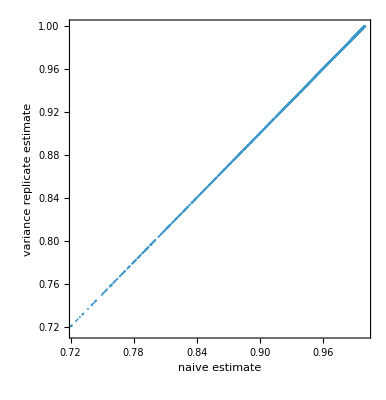

```mathematica
ListPlot[
Map[#["Value"]&,Values@Merge[{cvapProportionsNaive,cvapProportions},Identity],{2}],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"naive estimate","variance replicate estimate"}
]
```

But uncertainty is lower for

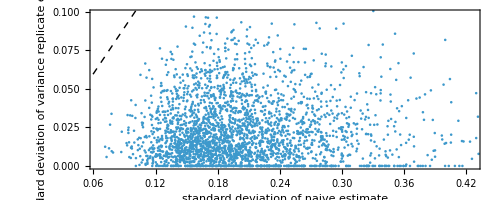

```mathematica
ListPlot[
Map[#["Uncertainty"]&,Values@Merge[{cvapProportionsNaive,cvapProportions},Identity],{2}],
AspectRatio->Automatic,
Epilog->{Dashed,InfiniteLine[{0,0},{1,1}]},
Frame->True,
FrameLabel->{"standard deviation of naive estimate","standard deviation of variance replicate estimate"}
]
```

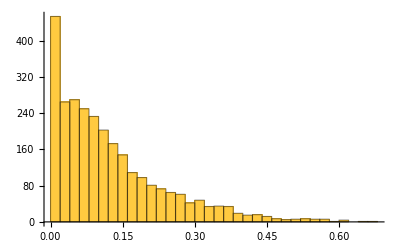

```mathematica
Histogram@Merge[{cvapProportionsNaive,cvapProportions},Apply[#2["Uncertainty"]/#1["Uncertainty"]&]]
```

## Plots for presentation

```mathematica
tractTotals=acsTracts[[All,Key[{"HispanicOrLatino","VAP"}]]];
```

```mathematica
blockTotals=categoryTotal[#,acsCategories["HispanicOrLatino"]]&/@decennialBlocks;
```

```mathematica
Length[tractTotals]
```

2796

```mathematica
Length[blockTotals]
```

232717

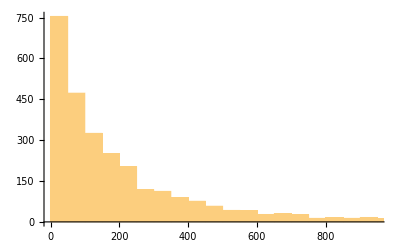

```mathematica
Histogram[tractTotals]
```

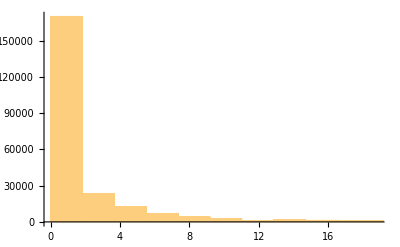

```mathematica
Histogram[blockTotals]
```

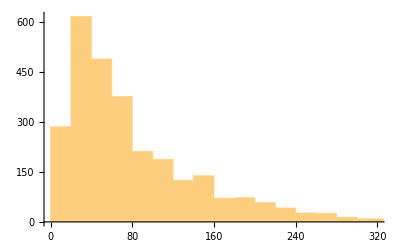

```mathematica
Histogram[Length/@GroupBy[Keys[decennialBlocks],geoidTract]]
```

```mathematica
Mean[Divide@@@DeleteCases[Values@Merge[KeyIntersection@{
categoryTotal[#,acsCategories["HispanicOrLatino"]]&/@decennialTracts,
tractTotals
},Identity],{_,0}]]//N
```

2.14111

```mathematica
N@Mean@Log[Divide@@@DeleteCases[Values@Merge[KeyIntersection@{
categoryTotal[#,acsCategories["HispanicOrLatino"]]&/@decennialTracts,
tractTotals
},Identity],{_,0}]]
```

0.29347

```mathematica
Total[Values[Merge[KeyIntersection@{
categoryTotal[#,acsCategories["HispanicOrLatino"]]&/@decennialTracts,
tractTotals
},Identity]]]
```

{742918,649092}

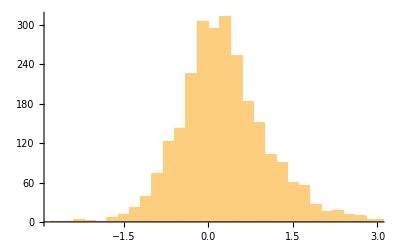

```mathematica
Histogram[Log[Divide@@@DeleteCases[Values@Merge[KeyIntersection@{
categoryTotal[#,acsCategories["HispanicOrLatino"]]&/@decennialTracts,
tractTotals
},Identity],{_,0}]]]
```

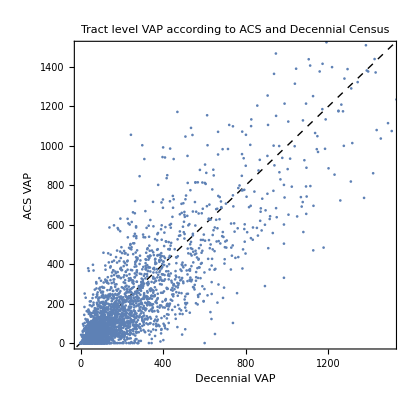

```mathematica
ListPlot[
Values@Merge[KeyIntersection@{
categoryTotal[#,acsCategories["HispanicOrLatino"]]&/@decennialTracts,
tractTotals
},Identity],
PlotRange->{{0,1500},{0,1500}},
PlotRangePadding->10,
PlotLabel->"Tract level VAP according to ACS and Decennial Census",
Frame->True,
FrameLabel->{"Decennial VAP","ACS VAP"},
AspectRatio->Automatic,
Epilog->{Dashed,InfiniteLine[{0,0},{1,1}]}
]
```

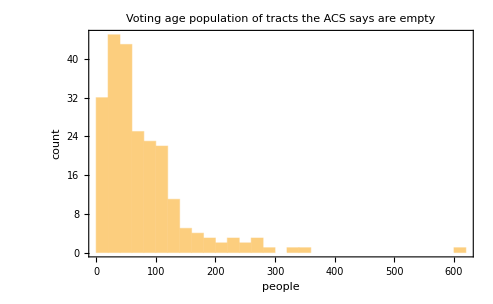

```mathematica
Histogram[
categoryTotal[#,acsCategories["HispanicOrLatino"]]&/@decennialTracts[[Keys@Select[tractTotals,EqualTo[0]]]],
PlotRange->All,
Frame->True,
FrameLabel->{"people","count"},
PlotLabel->"Voting age population of tracts the ACS says are empty"
]
```

```mathematica
emptyTractBlockPopulations=
With[{emptyTracts=Keys@Select[tractTotals,EqualTo[0]]},
categoryTotal[#,acsCategories["HispanicOrLatino"]]&/@decennialBlocks[[Select[Keys@decennialBlocks,MemberQ[emptyTracts,geoidTract[#]]&]]]
];//EchoTiming
```

4.17193

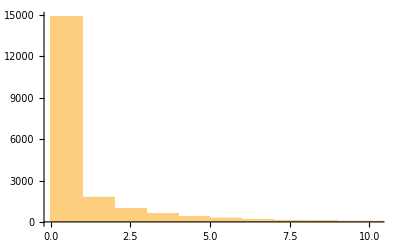

```mathematica
Histogram[emptyTractBlockPopulations]
```

### Aggregating to districts

```mathematica
dists=DeleteCases[
Lookup[
blockCVAPACS[[All,"HispanicOrLatino"]],
Select[blockDistrictPairs,MatchQ[{_,{"13","01"}}]][[All,1]]
],
BetaBinomialDistribution[_,_,0]
];
```

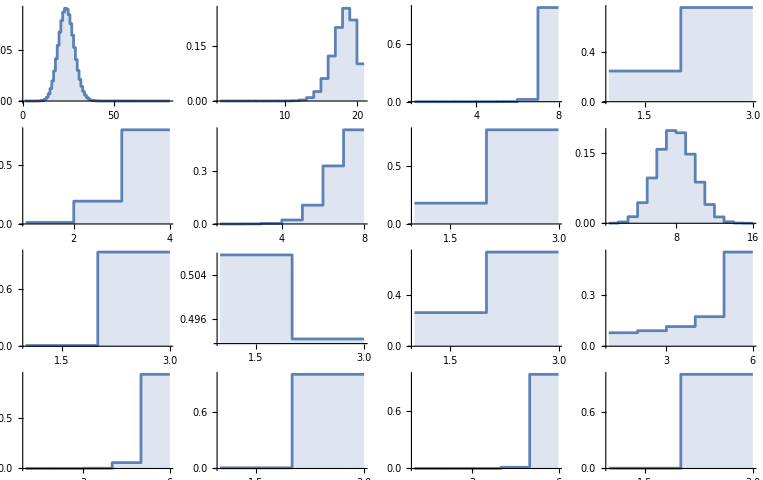
-Graphics-CVAP (people)pmf

```mathematica
Labeled[
GraphicsGrid[Partition[
ListLinePlot[
With[{pmf=betaBinomialPMF[#]},Append[pmf,Last[pmf]]],
PlotRange->All,
InterpolationOrder->0,
Filling->Bottom
]&/@RandomSample[SortBy[dists,Last],16],
4
]
],
{"CVAP (people)","pmf"},
{Bottom,Left},
RotateLabel->True
]
```

```mathematica
sumPMF=parallelFourierConvolveBetaBinomials[dists];//EchoTiming
```

6.71564

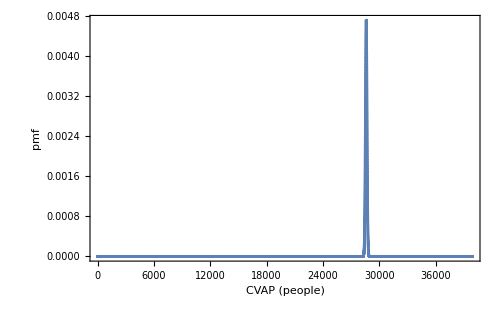

```mathematica
ListLinePlot[
sumPMF,
PlotRange->All,
InterpolationOrder->0,
Frame->True,
FrameLabel->{"CVAP (people)","pmf"},
ImageSize->500
]
```

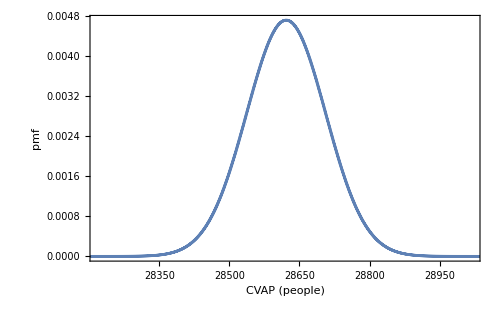

```mathematica
ListLinePlot[
sumPMF,
PlotRange->{{pmfQuantile[sumPMF,0.000001],pmfQuantile[sumPMF,0.999999]},All},
InterpolationOrder->0,
Frame->True,
FrameLabel->{"CVAP (people)","pmf"},
ImageSize->500
]
```

```mathematica
Solve[{
Mean[BinomialDistribution[n,p]]==μ,
Variance[BinomialDistribution[n,p]]==σ^2
},
{n,p}
]
```

{{n→μ^2/(μ-σ^2),p→(μ-σ^2)/μ}}

```mathematica
approxSumDistribution=NormalDistribution[Total[Mean/@dists],Sqrt@Total[Variance/@dists]]
```

NormalDistribution[28619.8,84.4063]

```mathematica
approxSumDistribution2=With[{
μ=Total[Mean/@dists],
σ=Sqrt@Total[Variance/@dists]
},
BinomialDistribution[Round[μ^2/(μ-σ^2)],(μ-σ^2)/μ]
]
```

BinomialDistribution[38105,0.751066]

```mathematica
approxSumDistribution3=With[{
μ=Total[Mean/@dists],
t=Total[dists[[All,3]]]
},
BinomialDistribution[t,μ/t]
]
```

BinomialDistribution[39938,0.716605]

General::munfl: Exp[-57481.5] is too small to represent as a normalized machine number; precision may be lost.

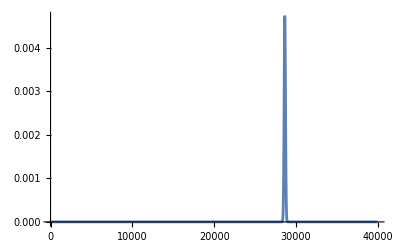

```mathematica
Plot[Evaluate@PDF[approxSumDistribution,x],{x,0,Total[dists[[All,3]]]}]
```

General::munfl: Exp[-52987.6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-52976.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-52965.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

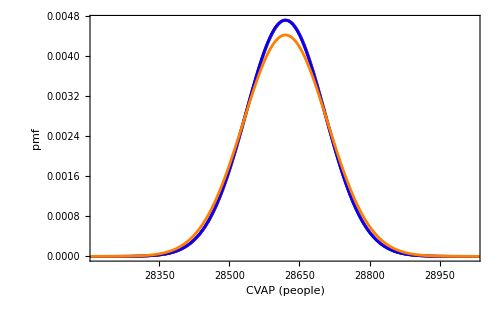

```mathematica
Show[{
ListLinePlot[
sumPMF,
PlotRange->{{pmfQuantile[sumPMF,0.000001],pmfQuantile[sumPMF,0.999999]},All},
DataRange->{0,Length[sumPMF]-1},
InterpolationOrder->0,
Frame->True,
FrameLabel->{"CVAP (people)","pmf"},
ImageSize->500
],
Plot[
Evaluate@PDF[approxSumDistribution,x],
{x,pmfQuantile[sumPMF,0.000001],pmfQuantile[sumPMF,0.999999]},
PlotStyle->Red
],
ListLinePlot[
PDF[approxSumDistribution2,Range[0,Length[sumPMF]-1]],
DataRange->{0,Length[sumPMF]-1},
PlotStyle->Blue
],
ListLinePlot[
PDF[approxSumDistribution3,Range[0,Length[sumPMF]-1]],
DataRange->{0,Length[sumPMF]-1},
PlotStyle->Orange
]
(*DiscretePlot[
Evaluate@PDF[approxSumDistribution3,x],
{x,pmfQuantile[sumPMF,0.000001],pmfQuantile[sumPMF,0.999999]},
PlotStyle->Blue
]*)
}]
```

General::munfl: Exp[-50358.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-50346.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-50336.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

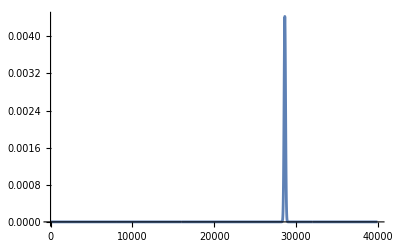

```mathematica
ListLinePlot@PDF[approxSumDistribution3,Range[0,Total[dists[[All,3]]]]]
```

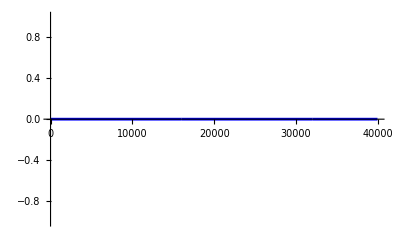

```mathematica
DiscretePlot[
Evaluate@PDF[approxSumDistribution2,x],
{x,0,Total@dists[[All,3]]},
PlotStyle->Blue
]
```

```mathematica
pmfQuantile[sumPMF,0.05]
```

28482

```mathematica
pmfQuantile[sumPMF,0.95]
```

28759

```mathematica
Quantile[approxSumDistribution,{0.05,0.95}]
```

{28480.9,28758.6}

```mathematica
Quantile[approxSumDistribution2,{0.05,0.95}]
```

General::munfl: 0.248934^38105 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-52976.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-52965.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{28480,28758}

```mathematica
Quantile[approxSumDistribution3,{0.05,0.95}]
```

General::munfl: 0.283395^39938 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-50346.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-50336.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{28472,28768}

## Validating race category conversion

```mathematica
decIntersectionEstimate=categoryTotal[#,Intersection[acsCategories["WhiteAlone"],acsCategories["HispanicOrLatino"]]]&/@decennialTracts;
```

```mathematica
acsIntersectionEstimate=acsTracts[[All,Key[{"WhiteAlone","VAP"}]]]-acsTracts[[All,Key[{"WhiteAloneNotHispanicOrLatino","VAP"}]]];
```

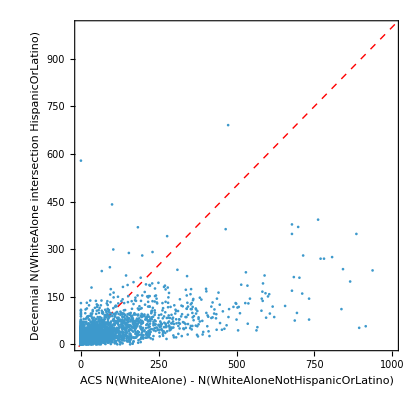

```mathematica
ListPlot[
Values@Merge[KeyIntersection@{acsIntersectionEstimate,decIntersectionEstimate},Identity],
Epilog->{Red,Dashed,InfiniteLine[{0,0},{1,1}]},
AspectRatio->Automatic,
PlotRange->{{0,1000},{0,1000}},
Frame->True,
FrameLabel->{"ACS N(WhiteAlone) - N(WhiteAloneNotHispanicOrLatino)","Decennial N(WhiteAlone intersection HispanicOrLatino)"}
]
```

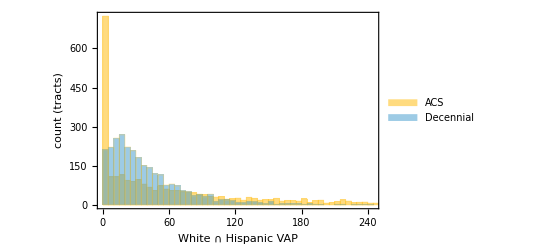

```mathematica
Histogram[
{acsIntersectionEstimate,decIntersectionEstimate},
{5},
Frame->True,
FrameLabel->{"White ∩ Hispanic VAP","count (tracts)"},
ChartLegends->{"ACS","Decennial"}
]
```

## TODO

### All possible constructions of litigation categories?

### Compare to special tabulation CVAP to test performance of category conversion strategies

```mathematica
acsCategories//Keys
```

{WhiteAlone,BlackOrAfricanAmericanAlone,AsianAlone,AmericanIndianAndAlaskaNativeAlone,NativeHawaiianAndOtherPacificIslanderAlone,SomeOtherRaceAlone,TwoOrMore,HispanicOrLatino,WhiteAloneNotHispanicOrLatino}